```mathematica
SetDirectory[NotebookDirectory[]];
<<bipartiteSUSY.m
```

```mathematica
(*This is a planar example*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 1,7](*+Subscript[X, 7,7]*),Subscript[X, 2,1](*+Subscript[X, 2,100]+Subscript[X, 3,1000]*),Subscript[X, 3,2](*+Subscript[X, 2,1]*)(*+Subscript[Z, 30]*),Subscript[X, 8,3](*+Subscript[X, 8,3]*),0,0,0},{Subscript[X, 13,1],Subscript[X, 1,4],0,0,Subscript[X, 4,13],0,0},{0,Subscript[X, 4,2],Subscript[X, 2,5],0,0,Subscript[X, 5,4],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,6],0,0,Subscript[X, 6,5]},{0,0,0,0,Subscript[X, 12,4],Subscript[X, 4,11],0},{0,0,0,0,0,Subscript[X, 11,5],Subscript[X, 5,10]},{0,0,0,Subscript[X, 6,9],0,0,Subscript[X, 10,6]}}/.formatrule;
bb={{0,0,0,Subscript[X, 7,8]},{0,0,0,0},{0,0,0,0},{0,0,0,0},{Subscript[X, 11,12],0,0,0},{0,Subscript[X, 10,11],0,0},{0,0,Subscript[X, 9,10],0}}/.formatrule;
cc={{Subscript[X, 7,13],0,0,0,0,0,0},{0,0,0,Subscript[X, 9,8],0,0,0},{0,0,0,0,Subscript[X, 13,12],0,0}}/.formatrule;
dd={{0,0,0,0},{0,0,0,0},{0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a non-planar example with secret poles*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 8,1],Subscript[X, 1,7](*+Subscript[X, 1,700]*),0,0,0,0},{0,Subscript[X, 2,1](*+Subscript[X, 2,100]*),0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}}/.formatrule;
bb={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}}/.formatrule;
cc={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}}/.formatrule;
dd={{0,0},{0,0},{0,0},{0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is another non-planar example with secret poles*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,9],0,Subscript[X, 6,3],0},{Subscript[X, 8,3],Subscript[X, 2,8],0,Subscript[X, 3,2]},{0,Subscript[X, 7,1],Subscript[X, 1,6],0},{0,Subscript[X, 1,2],Subscript[X, 5,1],Subscript[X, 2,4]},{0,0,Subscript[X, 3,5],Subscript[X, 4,3]}}/.formatrule;
bb={{Subscript[X, 9,6],0,0,0},{0,0,0,0},{0,Subscript[X, 6,7],0,0},{0,0,0,Subscript[X, 4,5]},{0,0,Subscript[X, 5,4],0}}/.formatrule;
cc={{Subscript[X, 9,8],0,0,0},{0,Subscript[X, 8,7],0,0}}/.formatrule;
dd={{0,0,0,0},{0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a non-planar example without secret poles*)
```

```mathematica
{aa,bb,cc,dd}={{{Subscript[Z, 10],Subscript[Z, 1],0,Subscript[Z, 7],0},{0,Subscript[Z, 12],Subscript[Z, 2],0,0},{0,Subscript[Z, 14],Subscript[Z, 15],0,Subscript[Z, 4]},{0,0,Subscript[Z, 16],Subscript[Z, 3],0},{Subscript[Z, 9],Subscript[Z, 18],0,0,Subscript[Z, 19]}},{{0,0,0},{Subscript[Z, 13],0,0},{0,0,0},{0,Subscript[Z, 17],0},{0,0,Subscript[Z, 5]}},{{Subscript[Z, 21],0,0,0,0},{0,0,0,Subscript[Z, 8],0},{0,0,0,0,Subscript[Z, 6]}},{{0,0,0},{0,0,0},{0,0,0}}}/.{Subscript[XX_, z1_]->XX[z1]};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is the normal square box*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 1,2],Subscript[X, 3,1]},{Subscript[X, 5,1],Subscript[X, 1,4]}};
bb={{Subscript[X, 2,3],0},{0,Subscript[X, 4,5]}};
cc={{Subscript[X, 2,5],0},{0,Subscript[X, 4,3]}};
dd={{0,0},{0,0}};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is the planar double square box*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,1],Subscript[X, 1,2],Subscript[X, 2,3]},{Subscript[X, 1,4],Subscript[X, 5,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2]}}/.formatrule;
bb={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,6],0}}/.formatrule;
cc={{0,0,Subscript[X, 3,6]},{Subscript[X, 4,3],0,0}}/.formatrule;
dd={{0,0},{0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Has 3 boundaries, but is reducible. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 7,1],Subscript[X, 1,6],0,0,0},{Subscript[X, 1,3],Subscript[X, 3,1],0,0,0},{Subscript[X, 3,7],0,Subscript[X, 4,3],Subscript[X, 7,4],0},{0,Subscript[X, 6,3],Subscript[X, 3,5],0,Subscript[X, 5,8]},{0,0,0,Subscript[X, 4,2],Subscript[X, 2,5]},{0,0,0,Subscript[X, 2,7],Subscript[X, 8,2]}}/.formatrule;
bb={{0,0,Subscript[X, 6,7],0,0},{Subscript[X, 3,3],0,0,0,0},{0,0,0,0,0},{0,0,0,0,Subscript[X, 8,6]},{0,Subscript[Y, 5,4],0,0,0},{0,0,0,Subscript[X, 7,8],0}}/.formatrule;
cc={{0,0,Subscript[X, 5,4],0,0}}/.formatrule;
dd={{0,0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Monster guy with intrinsically 3 boundaries.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 2,1],0,Subscript[X, 1,7],Subscript[X, 11,2],0,0,0,0,Subscript[X, 7,11],0,0,0,0,0,0},{Subscript[X, 1,3],Subscript[X, 4,1],0,0,Subscript[X, 3,11],Subscript[X, 11,4],0,0,0,0,0,0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0,Subscript[X, 5,11],Subscript[X, 11,6],0,0,0,0,0,0,0},{Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3],0,0,0,0,0,0,0,0,0,0},{0,Subscript[X, 5,4],0,0,0,Subscript[X, 4,9],Subscript[X, 9,5],0,0,0,0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0,0,Subscript[X, 6,10],Subscript[X, 10,7],0,0,0,0,0,0},{0,0,0,Subscript[X, 8,11],0,0,0,0,0,Subscript[X, 12,8],0,0,Subscript[X, 11,12],0,0},{0,0,0,0,Subscript[X, 11,8],0,0,0,0,Subscript[X, 8,13],0,0,Subscript[X, 13,11],0,0},{0,0,0,0,0,Subscript[X, 9,11],0,0,0,0,Subscript[X, 14,9],0,0,Subscript[X, 11,14],0},{0,0,0,0,0,0,Subscript[X, 11,9],0,0,0,Subscript[X, 9,15],0,0,Subscript[X, 15,11],0},{0,0,0,0,0,0,0,Subscript[X, 10,11],0,0,0,Subscript[X, 16,10],0,0,Subscript[X, 11,16]},{0,0,0,0,0,0,0,0,Subscript[X, 11,10],0,0,Subscript[X, 10,17],0,0,Subscript[X, 17,11]}}/.formatrule;
bb={{},{},{},{},{},{},{},{},{},{},{},{}}/.formatrule;
cc={{0,0,0,0,0,0,0,0,0,Subscript[X, 13,12],0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 12,13],0,0},{0,0,0,0,0,0,0,0,0,0,Subscript[X, 15,14],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 14,15],0},{0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 17,16],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 16,17]}}/.formatrule;
dd={{},{},{},{},{},{}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a dimer (no boundaries, genus 1)*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,4]+Subscript[X, 2,1],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]+Subscript[Y, 3,4]}}/.formatrule;
bb={{},{}};
cc={};
dd={};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a larger dimer (no boundaries, genus 1)*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,5],Subscript[X, 5,2],0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[Y, 3,5],0,Subscript[Y, 6,3]},{0,Subscript[X, 4,5],0,Subscript[Y, 5,2],Subscript[Y, 2,4],0},{0,0,Subscript[X, 6,4],0,Subscript[Y, 4,1],Subscript[Y, 1,6]}}/.formatrule;
bb={{},{},{},{},{},{}};
cc={};
dd={};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Y6,0 with TWO boundaries each cutting ONE line.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 1,2]+Subscript[X, 8,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 10,11],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}}/.formatrule;
bb={{0,0},{0,Subscript[X, 10,9]},{Subscript[X, 12,11],0},{0,0},{0,0},{0,0}}/.formatrule;
cc={{0,0,0,0,0,Subscript[Y, 12,11]},{0,0,0,0,Subscript[Y, 10,9],0}}/.formatrule;
dd={{0,0},{0,0}};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Subscript[bft, 29], i.e. the nonplanar G(3,6) example where secret poles first appear lower down in the stratification*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};

aa={{Subscript[X, 4,1],0,Subscript[X, 1,6],0,0,0},{Subscript[X, 2,4],Subscript[X, 5,2],0,0,0,0},{0,Subscript[X, 3,5],Subscript[X, 6,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 8,2],Subscript[X, 3,8]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}}/.formatrule;
bb={{Subscript[X, 6,4],0,0},{0,Subscript[X, 4,5],0},{0,0,Subscript[X, 5,6]},{0,0,0},{0,0,0},{0,0,0}}/.formatrule;
cc={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}}/.formatrule;
dd={{0,0,0},{0,0,0},{0,0,0}};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Standard example on a cylinder which reduces to sums of square boxes.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};

aa={{Subscript[X, 1,3],Subscript[X, 3,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,3],Subscript[X, 4,2]},{Subscript[X, 5,1],0,Subscript[X, 1,4]}}/.formatrule;
bb={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 3,4],0},{0,0,Subscript[X, 4,5]}}/.formatrule;
cc={{Subscript[X, 3,5],0,0}}/.formatrule;
dd={{0,0,0}};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is just like the nonplanar G(3,6) Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,6] and Subscript[X, 7,8], thus leaving some external nodes empty*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 4,1],0,Subscript[X, 1,4],0,0,0},{Subscript[X, 2,4],Subscript[X, 4,2],0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 7,2],Subscript[X, 3,7]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}}/.formatrule;
bb={{Subscript[X, 4,4],0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}/.formatrule;
cc={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,0,0},{0,0,0,0,0,Subscript[X, 7,9]}}/.formatrule;
dd={{0,0,0},{0,0,0},{0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}}/.formatrule;
bb={{},{},{},{}}/.formatrule;
cc={{0,0,0,0},{0,0,0,0}}/.formatrule;
dd={{},{}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes and an empty black node*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}}/.formatrule;
bb={{0},{0},{0},{0}}/.formatrule;
cc={{0,0,0,0},{0,0,0,0}}/.formatrule;
dd={{0},{0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is just like Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,2], Subscript[X, 6,4] and Subscript[X, 1,6] thus leaving us with no perfect matchings (as well as empty external nodes)*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 4,4],0,0,0,0,0},{Subscript[Y, 4,4],0,0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[Z, 4,4],0,0,Subscript[X, 7,4],Subscript[X, 4,7],0},{0,Subscript[Y, 4,3],0,0,Subscript[X, 8,4],Subscript[X, 3,8]},{0,0,Subscript[Y, 3,4],Subscript[X, 4,9],0,Subscript[X, 9,3]}}/.formatrule;
bb={{0,0,0},{0,0,0},{0,0,Subscript[W, 4,4]},{0,0,0},{0,0,0},{0,0,0}}/.formatrule;
cc={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}}/.formatrule;
dd={{0,0,0},{0,0,0},{0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a random large and vaguely "Kasteleyn-like" matrix*)
```

```mathematica
multiplier=2;
aa=Table[X[RandomInteger[100000],RandomInteger[100000]],{i,60multiplier},{j,60multiplier}];
bb=Table[Y[RandomInteger[100000],RandomInteger[100000]],{i,10multiplier},{j,60multiplier}];
cc=Table[Z[RandomInteger[100000],RandomInteger[100000]],{i,60multiplier},{j,15multiplier}];
dd=Table[0,{i,10multiplier},{j,15multiplier}];

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*These functions are NEW:           -------->     -------->     -------->     -------->     -------->     -------->  *)
```

```mathematica
getStratification[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,stratification,xlistandPmatrix,modulispace,startingplanarity,removable,topdim,varlist,makeDaughterGraphs,planarReducibility,tofixlevels,maxnonplanardimension,level,nonplanarpositions,planarboundaries,nonplanarboundaries,templevel,boundarykillededges,newplanarity,planarpositions,fix,identremovable,patternidentremovable,dim,locationofparents,thislevelspositions},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
(*We begin by making the face lattice of the matching polytope. Each element in the face lattice will be composed of three objects: the perfect matching matrix P, the moduli space/matroid polytope, and the answer to planarityQ. This will allow us to construct the face lattice while computing the perfect matchings and matrix P as few times as possible (not once per subgraph!)*)
(*We'll start with making the top-dimensional element. In P we shall also tag on which edges correspond to each row, by making the first element of each row the edge name*)
If[Dimensions[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]][[2]]===0,
stratification={};
,xlistandPmatrix=Join[Transpose[{Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]]}],getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph],2];
modulispace=moduliSpaceBFT[topleft,topright,bottomleft,bottomright,gauging,checkneeded,BFTgraph];
(*This will be the top-dimensional element in our stratification*)
startingplanarity=planarityQ[topleft,topright,bottomleft,bottomright];
If[BFTgraph||startingplanarity,
removable[0]={{xlistandPmatrix,modulispace,True}};
(*Since planarity is inherited by subgraphs, this means we'll never have to assess planarity again and we can treat everything as planar. This will mean we can assess reducibility very fast and easily, and identify everything according to their moduli space.*)
,removable[0]={{xlistandPmatrix,modulispace,startingplanarity}};
];
(*We'll save some basic information to avoid having to evaluate it many times*)
topdim=polytopeDim[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]];
varlist=Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]];
(*For each element in the face lattice, we will need to find all of its boundaries. These are found by deleting edges. makeDaughterGraphs takes an element in the face lattice and removes all possible edges, making potential boundaries (which will need to be verified). Initially the planarity of the subgraphs is inherited, i.e. is declared equal to the originating graph.*)
makeDaughterGraphs=Function[{boundaryelement},
Block[{pmat,moduli,elementplanarity,pmstokeep,daughters},
pmat=boundaryelement[[1]];
moduli=boundaryelement[[2]];
elementplanarity=boundaryelement[[3]];
pmstokeep=Table[Flatten[Position[boundaryelement[[1]][[jjj]],0,1]],{jjj,Length[pmat]}];
daughters=Table[{DeleteCases[pmat[[All,Prepend[pmstokeep[[jjj]],1]]],Prepend[ConstantArray[0,Length[pmstokeep[[jjj]]]],_]],moduli[[All,pmstokeep[[jjj]]-1]],elementplanarity},{jjj,Length[pmstokeep]}];
daughters
]
];
(*After making allsubgraphs, we'll keep only those whose dimension has decreased by one. Furthermore, since we're unltimately only interested in reduced graphs, we'll remove those that are reducible. planarReducibility is able to take a planar case and tell you its reducibility very fast.*)
planarReducibility=Function[{pmatrix,modulispace},
Block[{pmatrixtranspose,modulitranspose,pmatrixshort,reducib},
If[pmatrix==={},
reducib=True;
,pmatrixtranspose=Transpose[pmatrix];
If[modulispace==={},modulitranspose=Table[{0},Length[pmatrixtranspose]];,modulitranspose=Transpose[modulispace];];
pmatrixshort=Transpose[Map[Times@@pmatrixtranspose[[Flatten[Position[modulitranspose,#]]]]&,DeleteDuplicates[modulitranspose]]];
If[MemberQ[pmatrixshort,ConstantArray[0,Dimensions[pmatrixshort][[2]]]],reducib=True;,reducib=False;];];
reducib]
];
(*Now we'll go through each level, starting from the top-dimensional one and working our way down, and first contruct the face lattice, and then remove those elements which are reducible.*)
(*Sometimes a level only contains reducible boundaries. In these cases we'll eliminate the reducible examples in a second step*)
(*We'll start by assessing the reducibility of the starting point. If it's planar, we may use the fast way. Otherwise we'll need to use the dimension of the Grassmannian.*)
If[BFTgraph||startingplanarity,
If[planarReducibility[Drop[removable[0][[1,1]],None,{1}],removable[0][[1,2]]]===False,
tofixlevels={};
,tofixlevels={0};
];
,If[dimensionGrassmannian[topleft,topright,bottomleft,bottomright]===topdim,
tofixlevels={};
,tofixlevels={0};
];
];
(*We will only evaluate the Grassmannian dimension of those nonplanar diagrams that have a chance of not being reducible.*)
maxnonplanardimension=topdim;
For[level=1,level≤topdim,level++,
(*For each element in removable[level-1] we make all subgraphs. We'll end up with many duplicates. Since they all inherit their planarity, some subgraphs are simultaneously labelled planar=True as well as planar=False. If any of these labels is True, then the graph has come from a planar one and must hence be planar. If it's still labelled non-planar, we'll later use planarityQ to check whether this is still the case.*)
removable[level]=Map[{#[[1,1]],#[[1,2]],Or@@Map[Last,#]}&,GatherBy[Table[Sequence@@makeDaughterGraphs[removable[level-1][[iii]]],{iii,Length[removable[level-1]]}],First]];
(*Now we'll remove those elements whose dimension has decreased by too much*)
removable[level]=Cases[removable[level],zz_/;polytopeDim[Drop[zz[[1]],None,{1}]]===topdim-level];
(*On the surviving elements, we'll reassess planarity on the nonplanar cases.*)
nonplanarpositions=Flatten[Position[removable[level],{___,False}]];
templevel=removable[level];
(*Now we'll take the nonplanar cases and check whether they really are still nonplanar. Begin by turning each of these cases into a list of killed edges.*)
boundarykillededges=Map[#->0&,Map[Complement[varlist,#[[1,All,1]]]&,removable[level][[nonplanarpositions]]],{2}];
newplanarity=Map[planarityQ[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges];
templevel[[nonplanarpositions,3]]=newplanarity;
(*Now we know for sure that the planarity labelling is correct*)
(*We'll now want to only keep reduced elements. For planar cases, planarReducibility is very fast at deterining this. For nonplanar cases, we'll need to check whether the dimension of the Grassmannian is the same as that of P. If not, it means we have secretly reduced the dimension of the Grassmannian too much by creating a reducible graph.*)
planarpositions=Flatten[Position[templevel,{___,True}]];
nonplanarpositions=Flatten[Position[templevel,{___,False}]];
(*We'll put the reduced planar elements first, then the reduced non-planar ones*)
planarboundaries=Cases[templevel[[planarpositions]],zz_/;planarReducibility[Drop[zz[[1]],None,{1}],zz[[2]]]===False];
(*For the nonplanar boundaries we'll need to evluate the dimension of the Grassmannian. However, if at level=1 we already found that all nonplanar diagrams had at most dim(Grassmannian), the nonplanar diagrams at this level will not have a higher dimension than that. Hence, if that dimension is less than topdim-level, we do not even need to bother evaluating the Grassmannian*)
If[maxnonplanardimension≥topdim-level,
nonplanarboundaries=templevel[[nonplanarpositions]][[Flatten[Position[Map[dimensionGrassmannian[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges[[Flatten[Position[newplanarity,False]]]]],topdim-level]]]];
,nonplanarboundaries={};
];
removable[level]=Join[planarboundaries,nonplanarboundaries];
If[removable[level]==={},
(*If some level happens to only contain reducible examples, we'll keep all boundaries, and remove the reducible ones later.*)
removable[level]=templevel;
tofixlevels=Append[tofixlevels,level];
(*If we are the at the first level and there were no reduced boundaries, find out what the maximal dimension of the Grassmannian is for nonplanar diagrams, so that we don't need to evaluate it again until topdim-level is equal to this Grassmannian dimension.*)
If[level==1,
maxnonplanardimension=Max[Map[dimensionGrassmannian[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges[[Flatten[Position[newplanarity,False]]]]]];
];
];
];
For[fix=1,fix≤Length[tofixlevels],fix++,
removable[tofixlevels[[fix]]]={};
];
(*Now we'll identify boundaries according to their substratification. From each element, it's sufficient to check the substratification one level down, since everything below that has been vetted by this first substratification level. At the bottom level (zero-dimensional) we can identify everything according to their moduli space.*)
identremovable[topdim]=Map[#[[1,All,1]]&,GatherBy[removable[topdim],#[[2]]&],{2}];
(*In order to compute the substratifications in a fast way, we'll check which boundaries of one dimension higher have these as subsets. We can do this by writing 0-dim boundaries as {___,edge1,___,edge2,__...} and check which boundaries of one dimension high fit this pattern*)
patternidentremovable[topdim]=Map[Alternatives@@#&,Map[Riffle[#,___,{1,-1,2}]&,identremovable[topdim],{2}]];
(*We'll now go through each of the dimensions, starting from the bottom*)
If[BFTgraph||startingplanarity,
(*We can identify everything according to its moduli space*)
For[dim=1,dim<topdim,dim++,
identremovable[topdim-dim]=Map[#[[1,All,1]]&,GatherBy[removable[topdim-dim],Sort[DeleteDuplicates[Transpose[#[[2]]]]]&],{2}];
];
,(*we'll need to identify according to the substratifications*)
For[dim=1,dim<topdim,dim++,
(*Begin by turning the boundaries into lists of edges*)
removable[topdim-dim]=Map[#[[1,All,1]]&,removable[topdim-dim]];
(*For each of the sub-boundaries, we want to find which graphs of one dimension higher terminate in this sub-boundary*)
locationofparents=Map[Flatten[Position[removable[topdim-dim],#]]&,patternidentremovable[topdim-dim+1]];
(*In each of the elements in removable[topdim-dim], we now want to know where they are in the list of locationofparents.*)
(*Since locationofparents indexes according to position, we'll turn removable[topdim-dim] into positions first.*)
thislevelspositions=Range[Length[removable[topdim-dim]]];
identremovable[topdim-dim]=Map[removable[topdim-dim][[#]]&,GatherBy[thislevelspositions,Position[locationofparents,{___,#,___}]&],{2}];
(*Now we're ready to do the same thing for the next dimension, and will need patternidentremovable for this dimension*)
patternidentremovable[topdim-dim]=Map[Alternatives@@#&,Map[Riffle[#,___,{1,-1,2}]&,identremovable[topdim-dim],{2}]];
];
];
(*Finally, the top-dimensional level is simply the list of edges in the starting point*)
identremovable[0]=Map[{#[[1,All,1]]}&,removable[0]];
(*The stratification will be outputted as a list of elements, each containing all the boundaries of a certain dimensionality. Each boundary is expressed as a list of possible non-zero edges which are move-equivalent configurations, all representing the same boundary.*)
stratification=Table[identremovable[iii],{iii,0,topdim}];
];
,stratification=Null;
];
stratification
];
```

```mathematica
getStratificationNumbers[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,stratification,stratificationnumbers},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
stratification=getStratification[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph,gauging];
stratificationnumbers=Map[Length,stratification];
,stratificationnumbers=Null;
];
stratificationnumbers
];
```

```mathematica
getEulerNumber[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,eulernumber,stratificationnumbers},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
stratificationnumbers=getStratificationNumbers[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph,gauging];
eulernumber=Sum[Power[(-1),iii+1]stratificationnumbers[[-iii]],{iii,Length[stratificationnumbers]}];
,eulernumber=Null;
];
eulernumber
];
```

```mathematica
getFaceLattice[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,xlistandPmatrix,facelatticeboundaries,topdim,makeDaughterGraphs,level,facelattice},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
(*Each element in the face lattice of the matching polytope will be described by the perfect matching matrix P. This will allow us to construct the face lattice while computing the perfect matchings and matrix P as few times as possible (not once per subgraph!)*)
(*We'll start with making the top-dimensional element. In P we shall also tag on which edges correspond to each row, by making the first element of each row the edge name*)
xlistandPmatrix=Join[Transpose[{Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]]}],getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph],2];
(*This will be the top-dimensional element in our stratification*)
facelatticeboundaries[0]={xlistandPmatrix};
(*We'll save some basic information to avoid having to evaluate it many times*)
topdim=polytopeDim[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]];
(*For each element in the face lattice, we will need to find all of its boundaries. These are found by deleting edges. makeDaughterGraphs takes an element in the face lattice and removes all possible edges, making potential boundaries (which will need to be verified)*)
makeDaughterGraphs=Function[{boundaryelement},
Block[{pmat,pmstokeep,daughters},
pmat=boundaryelement;
pmstokeep=Table[Flatten[Position[boundaryelement[[jjj]],0,1]],{jjj,Length[pmat]}];
daughters=Table[DeleteCases[pmat[[All,Prepend[pmstokeep[[jjj]],1]]],Prepend[ConstantArray[0,Length[pmstokeep[[jjj]]]],_]],{jjj,Length[pmstokeep]}];
daughters
]
];
(*After making allsubgraphs, we'll keep only those whose dimension has decreased by one.*)
For[level=1,level≤topdim,level++,
(*For each element in removable[level-1] we make all subgraphs. We'll end up with many duplicates*)
facelatticeboundaries[level]=DeleteDuplicates[Table[Sequence@@makeDaughterGraphs[facelatticeboundaries[level-1][[iii]]],{iii,Length[facelatticeboundaries[level-1]]}]];
(*Now we'll remove those elements whose dimension has decreased by too much*)
facelatticeboundaries[level]=Cases[facelatticeboundaries[level],zz_/;polytopeDim[Drop[zz,None,{1}]]===topdim-level];
];
facelatticeboundaries[topdim]=DeleteCases[facelatticeboundaries[topdim],{}];
facelattice=Map[#[[All,1]]&,Table[facelatticeboundaries[iii],{iii,0,topdim}],{2}];
,facelattice=Null;
];
facelattice
];
```

```mathematica
getStratificationGraph[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,stratificationgraph,xlistandPmatrix,modulispace,startingplanarity,removable,topdim,varlist,makeDaughterGraphs,planarReducibility,tofixlevels,maxnonplanardimension,level,nonplanarpositions,templevel,boundarykillededges,newplanarity,planarpositions,planarboundaries,nonplanarboundaries,fix,identremovable,patternidentremovable,dim,locationofparents,thislevelspositions,identifiedboundaries,newlayer,alllayers,totalnumberofboundaries},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
(*We begin by making the face lattice of the matching polytope. Each element in the face lattice will be composed of three objects: the perfect matching matrix P, the moduli space/matroid polytope, and the answer to planarityQ. This will allow us to construct the face lattice while computing the perfect matchings and matrix P as few times as possible (not once per subgraph!)*)
(*We'll start with making the top-dimensional element. In P we shall also tag on which edges correspond to each row, by making the first element of each row the edge name*)
If[Dimensions[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]][[2]]===0,
stratificationgraph=AdjacencyGraph[{}];
,xlistandPmatrix=Join[Transpose[{Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]]}],getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph],2];
modulispace=moduliSpaceBFT[topleft,topright,bottomleft,bottomright,gauging,checkneeded,BFTgraph];
(*This will be the top-dimensional element in our stratification*)
startingplanarity=planarityQ[topleft,topright,bottomleft,bottomright];
If[BFTgraph||startingplanarity,
removable[0]={{xlistandPmatrix,modulispace,True}};
(*Since planarity is inherited by subgraphs, this means we'll never have to assess planarity again and we can treat everything as planar. This will mean we can assess reducibility very fast and easily, and identify everything according to their moduli space.*)
,removable[0]={{xlistandPmatrix,modulispace,startingplanarity}};
];
(*We'll save some basic information to avoid having to evaluate it many times*)
topdim=polytopeDim[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]];
varlist=Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]];
(*For each element in the face lattice, we will need to find all of its boundaries. These are found by deleting edges. makeDaughterGraphs takes an element in the face lattice and removes all possible edges, making potential boundaries (which will need to be verified). Initially the planarity of the subgraphs is inherited, i.e. is declared equal to the originating graph.*)
makeDaughterGraphs=Function[{boundaryelement},
Block[{pmat,moduli,elementplanarity,pmstokeep,daughters},
pmat=boundaryelement[[1]];
moduli=boundaryelement[[2]];
elementplanarity=boundaryelement[[3]];
pmstokeep=Table[Flatten[Position[boundaryelement[[1]][[jjj]],0,1]],{jjj,Length[pmat]}];
daughters=Table[{DeleteCases[pmat[[All,Prepend[pmstokeep[[jjj]],1]]],Prepend[ConstantArray[0,Length[pmstokeep[[jjj]]]],_]],moduli[[All,pmstokeep[[jjj]]-1]],elementplanarity},{jjj,Length[pmstokeep]}];
daughters
]
];
(*After making allsubgraphs, we'll keep only those whose dimension has decreased by one. Furthermore, since we're unltimately only interested in reduced graphs, we'll remove those that are reducible. planarReducibility is able to take a planar case and tell you its reducibility very fast.*)
planarReducibility=Function[{pmatrix,modulispace},
Block[{pmatrixtranspose,modulitranspose,pmatrixshort,reducib},
If[pmatrix==={},
reducib=True;
,pmatrixtranspose=Transpose[pmatrix];
If[modulispace==={},modulitranspose=Table[{0},Length[pmatrixtranspose]];,modulitranspose=Transpose[modulispace];];
pmatrixshort=Transpose[Map[Times@@pmatrixtranspose[[Flatten[Position[modulitranspose,#]]]]&,DeleteDuplicates[modulitranspose]]];
If[MemberQ[pmatrixshort,ConstantArray[0,Dimensions[pmatrixshort][[2]]]],reducib=True;,reducib=False;];];
reducib]
];
(*Now we'll go through each level, starting from the top-dimensional one and working our way down, and first contruct the face lattice, and then remove those elements which are reducible.*)
(*Sometimes a level only contains reducible boundaries. In these cases we'll eliminate the reducible examples in a second step*)
(*We'll start by assessing the reducibility of the starting point. If it's planar, we may use the fast way. Otherwise we'll need to use the dimension of the Grassmannian.*)
If[BFTgraph||startingplanarity,
If[planarReducibility[Drop[removable[0][[1,1]],None,{1}],removable[0][[1,2]]]===False,
tofixlevels={};
,tofixlevels={0};
];
,If[dimensionGrassmannian[topleft,topright,bottomleft,bottomright]===topdim,
tofixlevels={};
,tofixlevels={0};
];
];
(*We will only evaluate the Grassmannian dimension of those nonplanar diagrams that have a chance of not being reducible.*)
maxnonplanardimension=topdim;
For[level=1,level≤topdim,level++,
(*For each element in removable[level-1] we make all subgraphs. We'll end up with many duplicates. Since they all inherit their planarity, some subgraphs are simultaneously labelled planar=True as well as planar=False. If any of these labels is True, then the graph has come from a planar one and must hence be planar. If it's still labelled non-planar, we'll later use planarityQ to check whether this is still the case.*)
removable[level]=Map[{#[[1,1]],#[[1,2]],Or@@Map[Last,#]}&,GatherBy[Table[Sequence@@makeDaughterGraphs[removable[level-1][[iii]]],{iii,Length[removable[level-1]]}],First]];
(*Now we'll remove those elements whose dimension has decreased by too much*)
removable[level]=Cases[removable[level],zz_/;polytopeDim[Drop[zz[[1]],None,{1}]]===topdim-level];
(*On the surviving elements, we'll reassess planarity on the nonplanar cases.*)
nonplanarpositions=Flatten[Position[removable[level],{___,False}]];
templevel=removable[level];
(*Now we'll take the nonplanar cases and check whether they really are still nonplanar. Begin by turning each of these cases into a list of killed edges.*)
boundarykillededges=Map[#->0&,Map[Complement[varlist,#[[1,All,1]]]&,removable[level][[nonplanarpositions]]],{2}];
newplanarity=Map[planarityQ[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges];
templevel[[nonplanarpositions,3]]=newplanarity;
(*Now we know for sure that the planarity labelling is correct*)
(*We'll now want to only keep reduced elements. For planar cases, planarReducibility is very fast at deterining this. For nonplanar cases, we'll need to check whether the dimension of the Grassmannian is the same as that of P. If not, it means we have secretly reduced the dimension of the Grassmannian too much by creating a reducible graph.*)
planarpositions=Flatten[Position[templevel,{___,True}]];
nonplanarpositions=Flatten[Position[templevel,{___,False}]];
(*We'll put the reduced planar elements first, then the reduced non-planar ones*)
planarboundaries=Cases[templevel[[planarpositions]],zz_/;planarReducibility[Drop[zz[[1]],None,{1}],zz[[2]]]===False];
(*For the nonplanar boundaries we'll need to evluate the dimension of the Grassmannian. However, if at level=1 we already found that all nonplanar diagrams had at most dim(Grassmannian), the nonplanar diagrams at this level will not have a higher dimension than that. Hence, if that dimension is less than topdim-level, we do not even need to bother evaluating the Grassmannian*)
If[maxnonplanardimension≥topdim-level,
nonplanarboundaries=templevel[[nonplanarpositions]][[Flatten[Position[Map[dimensionGrassmannian[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges[[Flatten[Position[newplanarity,False]]]]],topdim-level]]]];
,nonplanarboundaries={};
];
removable[level]=Join[planarboundaries,nonplanarboundaries];
If[removable[level]==={},
(*If some level happens to only contain reducible examples, we'll keep all boundaries, and remove the reducible ones later.*)
removable[level]=templevel;
tofixlevels=Append[tofixlevels,level];
(*If we are the at the first level and there were no reduced boundaries, find out what the maximal dimension of the Grassmannian is for nonplanar diagrams, so that we don't need to evaluate it again until topdim-level is equal to this Grassmannian dimension.*)
If[level==1,
maxnonplanardimension=Max[Map[dimensionGrassmannian[topleft/.#,topright/.#,bottomleft/.#,bottomright]&,boundarykillededges[[Flatten[Position[newplanarity,False]]]]]];
];
];
];
For[fix=1,fix≤Length[tofixlevels],fix++,
removable[tofixlevels[[fix]]]={};
];
(*Now we'll identify boundaries according to their substratification. From each element, it's sufficient to check the substratification one level down, since everything below that has been vetted by this first substratification level. At the bottom level (zero-dimensional) we can identify everything according to their moduli space.*)
identremovable[topdim]=Map[#[[1,All,1]]&,GatherBy[removable[topdim],#[[2]]&],{2}];
(*In order to compute the substratifications in a fast way, we'll check which boundaries of one dimension higher have these as subsets. We can do this by writing 0-dim boundaries as {___,edge1,___,edge2,__...} and check which boundaries of one dimension high fit this pattern*)
patternidentremovable[topdim]=Map[Alternatives@@#&,Map[Riffle[#,___,{1,-1,2}]&,identremovable[topdim],{2}]];
(*We'll go through each dimension. When we find the connectivity between the various dimensions, we'll store it in an adjacencymatrix format. At then end we'll turn this information into a stratification graph.*)
For[dim=1,dim<topdim,dim++,
(*Begin by turning the boundaries into lists of edges*)
removable[topdim-dim]=Map[#[[1,All,1]]&,removable[topdim-dim]];
(*For each of the sub-boundaries, we want to find which graphs of one dimension higher terminate in this sub-boundary*)
locationofparents=Map[Flatten[Position[removable[topdim-dim],#]]&,patternidentremovable[topdim-dim+1]];
(*In each of the elements in removable[topdim-dim], we now want to know where they are in the list of locationofparents.*)
(*Since locationofparents indexes according to position, we'll turn removable[topdim-dim] into positions first.*)
thislevelspositions=Range[Length[removable[topdim-dim]]];
identifiedboundaries=GatherBy[thislevelspositions,Position[locationofparents,{___,#,___}]&];
identremovable[topdim-dim]=Map[removable[topdim-dim][[#]]&,identifiedboundaries,{2}];
(*Now we're ready to do the same thing for the next dimension, and will need patternidentremovable for this dimension*)
patternidentremovable[topdim-dim]=Map[Alternatives@@#&,Map[Riffle[#,___,{1,-1,2}]&,identremovable[topdim-dim],{2}]];
(*Now we'll make a matrix with rows corresponding to boundaries in removable[topdim-dim] and columns corresponding to boundaries in identremovable[topdim-dim+1]. If an object in removable[topdim-dim] can access a subboundary in identremovable[topdim-dim+1] that entry has a 1, otherwise it is 0.*)
newlayer[dim]=Normal[SparseArray[Map[#->1&,MapThread[Sequence@@Transpose[{#1,ConstantArray[#2,Length[#1]]}]&,{locationofparents,Range[Length[locationofparents]]}]]]];
(*After the identifications many objects in removable[topdim-dim] are declared to be the same. We'll therefore only select one representative from each such equivalence class of graphs.*)
newlayer[dim]=newlayer[dim][[Complement[Range[Length[removable[topdim-dim]]],Map[Sequence@@Delete[#,1]&,identifiedboundaries]]]];
];
(*In the final layer, we have the top-dimensional elements going to the codimension-1 elements. Since the top-dim elements are not connected to themselves in the stratification, we must add some zeros in front of newlayer[topdim-1], so that the adjacency matrix is correct.*)
newlayer[topdim-1]=Join[Table[0,{iii,Length[newlayer[topdim-1]]},{jjj,Length[newlayer[topdim-1]]}],newlayer[topdim-1],2];
alllayers=Reverse[Table[newlayer[iii],{iii,1,topdim-1}]];
totalnumberofboundaries=Total[Map[Dimensions[#][[2]]&,alllayers]];
stratificationgraph=AdjacencyGraph[Normal[SparseArray[Band[{1,1}]->alllayers,{totalnumberofboundaries,totalnumberofboundaries}]]];
];
,stratificationgraph=Null;
];
stratificationgraph
];
```

```mathematica
getFaceLatticeGraph[topleft_,topright_,bottomleft_,bottomright_,checkneeded_:False,BFTgraph_:False,gauging_:2]/;(gauging===1&&BFTgraph===True||gauging===2):=Block[{checkOK,xlistandPmatrix,facelatticeboundaries,topdim,makeDaughterGraphs,level,patternfacelatticeboundaries,locationofparents,newlayer,alllayers,totalnumberofboundaries,stratificationgraph},
checkOK=True;
If[checkneeded==True,
checkOK=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[checkOK==True,
(*Each element in the face lattice of the matching polytope will be described by the perfect matching matrix P. This will allow us to construct the face lattice while computing the perfect matchings and matrix P as few times as possible (not once per subgraph!)*)
(*We'll start with making the top-dimensional element. In P we shall also tag on which edges correspond to each row, by making the first element of each row the edge name*)
If[Dimensions[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]][[2]]===0,
stratificationgraph=AdjacencyGraph[{}];
,xlistandPmatrix=Join[Transpose[{Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]]}],getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph],2];
(*This will be the top-dimensional element in our stratification*)
facelatticeboundaries[0]={xlistandPmatrix};
(*We'll save some basic information to avoid having to evaluate it many times*)
topdim=polytopeDim[getPmatrix[topleft,topright,bottomleft,bottomright,checkneeded,BFTgraph]];
(*For each element in the face lattice, we will need to find all of its boundaries. These are found by deleting edges. makeDaughterGraphs takes an element in the face lattice and removes all possible edges, making potential boundaries (which will need to be verified)*)
makeDaughterGraphs=Function[{boundaryelement},
Block[{pmat,pmstokeep,daughters},
pmat=boundaryelement;
pmstokeep=Table[Flatten[Position[boundaryelement[[jjj]],0,1]],{jjj,Length[pmat]}];
daughters=Table[DeleteCases[pmat[[All,Prepend[pmstokeep[[jjj]],1]]],Prepend[ConstantArray[0,Length[pmstokeep[[jjj]]]],_]],{jjj,Length[pmstokeep]}];
daughters
]
];
(*After making allsubgraphs, we'll keep only those whose dimension has decreased by one.*)
For[level=1,level≤topdim,level++,
(*For each element in removable[level-1] we make all subgraphs. We'll end up with many duplicates*)
facelatticeboundaries[level]=DeleteDuplicates[Table[Sequence@@makeDaughterGraphs[facelatticeboundaries[level-1][[iii]]],{iii,Length[facelatticeboundaries[level-1]]}]];
(*Now we'll remove those elements whose dimension has decreased by too much*)
facelatticeboundaries[level]=Cases[facelatticeboundaries[level],zz_/;polytopeDim[Drop[zz,None,{1}]]===topdim-level];
];
facelatticeboundaries[topdim]=DeleteCases[facelatticeboundaries[topdim],{}];
facelatticeboundaries[0]=Map[#[[All,1]]&,facelatticeboundaries[0]];
(*We'll go through each level of the stratification. When we find the connectivity between the various dimensions, we'll store it in an adjacencymatrix format. At then end we'll turn this information into a stratification graph.*)
For[level=1,level≤topdim,level++,
(*Begin by turning the boundaries into lists of edges*)
facelatticeboundaries[level]=Map[#[[All,1]]&,facelatticeboundaries[level]];
(*For each of the sub-boundaries, we want to find which graphs of one dimension higher terminate in this sub-boundary*)
(*In order to compute the substratifications in a fast way, we'll check which boundaries of one dimension higher have these as subsets. We can do this by writing 0-dim boundaries as {___,edge1,___,edge2,__...} and check which boundaries of one dimension high fit this pattern*)
patternfacelatticeboundaries[level]=Map[Riffle[#,___,{1,-1,2}]&,facelatticeboundaries[level]];
(*In each of the elements in removable[topdim-dim], we now want to know where they are in the list of locationofparents.*)
locationofparents=Map[Flatten[Position[facelatticeboundaries[level-1],#]]&,patternfacelatticeboundaries[level]];
(*Now we'll make a matrix with rows corresponding to boundaries in removable[topdim-dim] and columns corresponding to boundaries in identremovable[topdim-dim+1]. If an object in removable[topdim-dim] can access a subboundary in identremovable[topdim-dim+1] that entry has a 1, otherwise it is 0.*)
newlayer[level]=Normal[SparseArray[Map[#->1&,MapThread[Sequence@@Transpose[{#1,ConstantArray[#2,Length[#1]]}]&,{locationofparents,Range[Length[locationofparents]]}]]]];
];
newlayer[1]=Join[Table[0,{iii,Length[newlayer[1]]},{jjj,Length[newlayer[1]]}],newlayer[1],2];
alllayers=Table[newlayer[iii],{iii,1,topdim}];
totalnumberofboundaries=Total[Map[Dimensions[#][[2]]&,alllayers]];
stratificationgraph=AdjacencyGraph[Normal[SparseArray[Band[{1,1}]->alllayers,{totalnumberofboundaries,totalnumberofboundaries}]]];
];
,stratificationgraph=Null;
];
stratificationgraph
];
```

```mathematica
(*These functions are OLD:           -------->     -------->     -------->     -------->     -------->     -------->  *)
```

```mathematica
graphy=getFaceLatticeGraph[topleft,topright,bottomleft,bottomright];
```

```mathematica
(*THIS IS A GOOD WAY TO FIND NON-PLUCKER POLES*)
```

```mathematica
ii=75;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

a=a/.{X[2,5]->0};
b=b/.{X[2,5]->0};
c=c/.{X[2,5]->0};
Cmat=pathMatrix[a,b,c,d];
allorder3relations=Map[Equal@@#&,DeleteCases[Map[#/(Intersection@@#)&,Subsets[Map[Times@@#&,Subsets[Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],{3}]],{2}]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a,b,c,d],0]]]],{___,0,___}]];
currentpluckerrelations=Map[Simplify,pluckerRelations[Length[Cmat],Dimensions[Cmat][[2]]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a,b,c,d],0]]]]];
secretorder3relations=DeleteCases[ParallelMap[Simplify,allorder3relations],Alternatives@@currentpluckerrelations];
hihi=MapThread[Rule,{Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],(minorsAsPerfectMatchings[a,b,c,d])}];
numberofsecretrelations=Count[ParallelMap[Expand[#/.hihi]===True&,secretorder3relations],True];
numberofsecretrelations
```

```mathematica
(*These functions TEST NEW GRAPH FUNCTIONALITY*)
```

```mathematica
aa={{Subscript[X, 8,1],Subscript[X, 1,7],0,0,0,0},{0,Subscript[X, 2,1],0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}};
bb={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
cc={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}};
dd={{0,0},{0,0},{0,0},{0,0}};
```

```mathematica
a=aa/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
b=bb/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
c=cc/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
d=dd/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
```

```mathematica
jakemoduliGauging2[a,b,c,d];
```

```mathematica
P
```

{{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0},{0,1,1,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,1,1,1,0,0,1,0,1,1},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1},{0,0,1,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,1,1,0,0,0,0,0,1,1,0,1,0,0},{0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,1,0,0,0,0,0,1,0},{1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0}}

```mathematica
Gmoduli
```

{{1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0}}

```mathematica
reducibility[P,Gmoduli]
```

True

```mathematica
BFTdim[P]
```

9

```mathematica
reduction[P,Gmoduli,1]
```

Level is 1 and we have to check 20 guys.

Level is 2 and we have to check 1 guys.

Can remove 1 legs in 2 different ways.

Sets of legs that can be Higgsed are 'higgslist'= {{Z_6},{Z_19}}

```mathematica
higgs[Subscript[Z, 6],Xlist,P,Gmoduli]
```

After killing Z_6 the Master space has dimension 8 and the moduli space has dimension 5 .

The new P matrix is saved under 'Phiggs'. New moduli space under 'Gmodulihiggs'. New Xlist under 'Xlisthiggs'.

```mathematica
reducibility[Phiggs,Gmodulihiggs]
```

False

```mathematica
BFTdim[Phiggs]
```

8

```mathematica
PlanarGraphQ[-Graphics-]
```

True

```mathematica
<<GraphUtilities`
```

VertexList::graph: A graph object is expected at position 1 in VertexList[{}].

VertexList::graph: A graph object is expected at position 1 in VertexList[1].

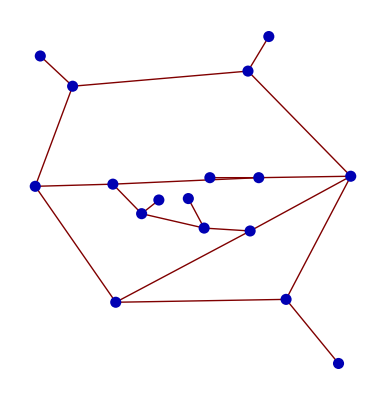
{-Graphics-,Graph→{1→2,1→3,2→4,1→5,5→6,6→7,7→8,8→2,7→9,5→10,6→11,11→8,8→12,12→13,12→10,11→14,14→15,15→10,15→16,14→17},Coordinates→{{122,681},{366,702},{77,723},{395,750},{70,542},{182,381},{419,385},{509,556},{492,296},{178,545},{369,480},{381,554},{313,554},{305,484},{218,504},{242,523},{283,525}},VertexLabels→{1,2,3,3,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}}

```mathematica
GraphEdit[]
```

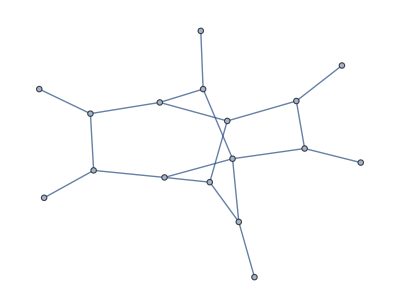

```mathematica
UndirectedGraph[Graph[{1->2,1->3,2->4,1->5,5->6,6->7,7->8,8->2,7->9,5->10,6->11,11->8,8->12,12->13,12->10,11->14,14->15,15->10,15->16,14->17}]]
```

```mathematica
hahas=RandomGraph[{100,90},10];
For[gi=1,gi<Length[hahas]+1,gi++,
Print[AbsoluteTiming[PlanarGraphQ[hahas[[gi]]]]];
];
```

{0.000136843,True}

{0.000197852,False}

{0.000197282,False}

{0.000154518,False}

{0.000151668,False}

{0.000150527,False}

{0.000184738,True}

{0.000182457,False}

{0.000149957,True}

{0.000140834,False}

```mathematica
9!Mean[{0.00013684289751151192,0.00019785202265206096,0.00019728184391242968,0.0001545184384400822,0.0001516675447419257,0.0001505271872626631,0.00018473791164054108,0.00018245719668201588,0.0001499570085230318,0.00014083414868893101}]
```

59.7546

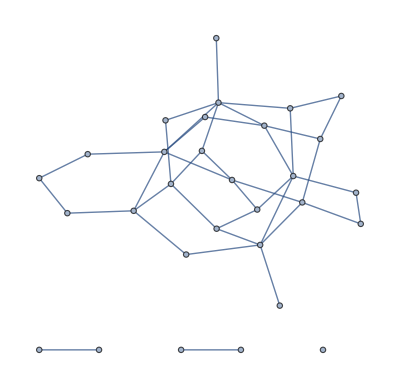
```mathematica
haha=-Graphics-;
```

```mathematica
PlanarGraphQ[haha]//AbsoluteTiming
```

{0.0000843865,False}

Here is all of the code in allBFTfunctions

```mathematica
(*To calculate the dimension of a polytope*)
(*BFTdim[mat_]:=Block[{newsp,gi,dim},If[MemberQ[Transpose[mat],ConstantArray[0,Length[mat]]],
dim=MatrixRank[mat];
,newsp=mat;
For[gi=1,gi<Dimensions[mat][[2]]+1,gi++,
newsp[[All,gi]]=newsp[[All,gi]]-mat[[All,1]];
];
dim=MatrixRank[newsp];
];dim]*)

(*DONE, NOW CALLED polytopeDim*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*To obtain the coordinates of a polytope, with the shift such that one vertex is at the origin.*)
(*polytope[mat_]:=Block[{newsp,gi},
newsp=mat;
If[FreeQ[Transpose[mat],ConstantArray[0,Length[mat]]],
For[gi=1,gi<Dimensions[mat][[2]]+1,gi++,
newsp[[All,gi]]=newsp[[All,gi]]-mat[[All,1]];
];
];
newsp=DeleteCases[RowReduce[newsp],ConstantArray[0,Dimensions[mat][[2]]]];
newsp]*)

(*SKIPPED*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Calculates the contour integral circled at infinity (takes into account all poles)*)
(*contourint[func_,var_]:=Block[{sols,tot,i},
sols=Solve[Denominator[func]==0,var];
sols=DeleteDuplicates[Sequence@@@(sols/.{Rule->List})];
tot=0;
For[i=1,i<Length[sols]+1,i++,
tot=tot+2Pi I Residue[func,sols[[i]]];
];
tot
]*)

(*SKIPPED*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives you the total number of faces.*)
(*totFaces[a_,b_,c_,d_]:=Block[{K0full,K0flatX,facelist,i,nf},
K0full=Join[Join[a,c],Join[b,d],2];
K0flatX=DeleteCases[Flatten[K0full],0];
K0flatX=Sequence@@@(MapThread[MonomialList,{K0flatX}]);
facelist={};
For[i=1,i<Length[K0flatX]+1,i++,
facelist=Join[facelist,{sub1[K0flatX[[i]]]}];
facelist=Join[facelist,{sub2[K0flatX[[i]]]}];
];
facelist=DeleteDuplicates[facelist];
nf=Length[facelist];
nf
]*)

(*DONE, SAME NAME*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives you the number of external faces.*)
(*externalFaces[a_,b_,c_,d_]:=Block[{flatext,extfacelist,i,extn},
flatext=DeleteCases[Join[Flatten[b],Flatten[c]],0];
flatext=Sequence@@@(MapThread[MonomialList,{flatext}]);
extfacelist={};
For[i=1,i<Length[flatext]+1,i++,
extfacelist=Join[extfacelist,{sub1[flatext[[i]]]}];
extfacelist=Join[extfacelist,{sub2[flatext[[i]]]}];
];
extfacelist=DeleteDuplicates[extfacelist];
extn=Length[extfacelist];
extn
]*)

(*DONE, SAME NAME*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives you the number of internal faces.*)
(*internalFaces[a_,b_,c_,d_]:=Block[{intn},
intn=totFaces[a,b,c,d]-externalFaces[a,b,c,d];
intn
]*)

(*DONE, SAME NAME*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives True if "fullspace" is reducible, or False if it isn't. Fullspace is in the form of the perfect matching matrix P.*)
(*reducibility[fullspace_,moduli_]:=Block[{coordi,red,columnlist,po,ps,Pshort},(*First need to find out which columns are the same point in the moduli space*)
coordi=DeleteDuplicates[Transpose[moduli]];
columnlist={};
For[po=1,po<Length[coordi]+1,po++,
columnlist=Join[columnlist,Transpose[Position[Transpose[moduli],coordi[[po]]]]];
];(*Now we know which columns represent the same point in the toric diagram!*)
Pshort=Table[0,{x,Length[fullspace]},{y,Length[columnlist]}];
For[ps=1,ps<Length[columnlist]+1,ps++,
Pshort[[All,ps]]=Product[fullspace[[All,columnlist[[ps,i]]]],{i,Length[columnlist[[ps]]]}];
];
If[MemberQ[Pshort,ConstantArray[0,Dimensions[Pshort][[2]]]],red=True,red=False];
red
]*)

(*DONE! NOW CALLED reducibilityBFTQ*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Draws the graph in a way that is as planar as possible to help you to work out how many boundaries it must have, and whether it can be drawn on a genus zero surface.*)
(*planarity[a_,b_,c_,d_]:=Block[{kasta,bigamat,multiguys,newbigamat,nu,tofix,coltoadd,rowtoadd,du,graph},
kasta=Join[Join[a,c],Join[b,d],2];
(*Now make the weighted adjacency matrix*)
bigamat=Join[Join[Table[0,{x,Length[kasta]},{y,Length[kasta]}],Transpose[kasta]],Join[kasta,Table[0,{x,Dimensions[kasta][[2]]},{y,Dimensions[kasta][[2]]}]],2];
multiguys=DeleteDuplicates[MapThread[Sort,{Position[MapThread[Length,{MonomialList[bigamat]},2],x_/;x>1]}]];
newbigamat=bigamat;
For[nu=1,nu<Length[multiguys]+1,nu++,
tofix=MonomialList[bigamat[[multiguys[[nu]][[1]],multiguys[[nu]][[2]]]]];
(*we'll now need to add a certain number of columns and rows, so that multiedges get their own node at the midway point, and hence don't overlap.*)
coltoadd=Table[0,{x,Length[newbigamat]},{y,Length[tofix]-1}];
For[du=2,du<Length[tofix]+1,du++,
coltoadd[[multiguys[[nu]][[1]],du-1]]=tofix[[du]];
coltoadd[[multiguys[[nu]][[2]],du-1]]=tofix[[du]]
];
rowtoadd=Table[0,{x,Length[tofix]-1},{y,Dimensions[newbigamat][[2]]+Length[tofix]-1}];
For[du=2,du<Length[tofix]+1,du++,
rowtoadd[[du-1,multiguys[[nu]][[1]]]]=tofix[[du]];
rowtoadd[[du-1,multiguys[[nu]][[2]]]]=tofix[[du]]
];
newbigamat=Join[newbigamat,coltoadd,2];
newbigamat=Join[newbigamat,rowtoadd];
newbigamat[[multiguys[[nu]][[1]],multiguys[[nu]][[2]]]]=tofix[[1]];
newbigamat[[multiguys[[nu]][[2]],multiguys[[nu]][[1]]]]=tofix[[1]];
];
newbigamat=newbigamat/.{0->∞};
graph=WeightedAdjacencyGraph[newbigamat];
If[PlanarGraphQ[graph],
Print["The graph can be written in a genus 0 surface, i.e. the plane with a certain number of boundaries."];
,Print["The graph CANNOT be written in a genus 0 surface! You have genus > 0 ."]];
Print["This is the graph as Mathematica preferes to draw it (usually Mathematica preferes to draw it without crossings, so the presence of crossings is usually an indicator for nonplanarity):"];
Print[WeightedAdjacencyGraph[newbigamat,VertexLabels->"Name"]];
Print["This is the graph when Mathematica has been explicitly told to avoid edge crossings (Mathematica will usually try and do it with the smallest number of boundaries):"];
Print[WeightedAdjacencyGraph[newbigamat,GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImagePadding->20]];
]*)

(*DONE, NOW CALLED planarityQ*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Draws the bipartite graph associated to the Kasteleyn matrix*)
(*drawBFT[a_,b_,c_,d_]:=Block[{kasta,bigamat,multiguys,newbigamat,nu,tofix,coltoadd,rowtoadd,du,edgelabs,colors,ai,aj},
kasta=Join[Join[a,c],Join[b,d],2];
(*Now make the weighted adjacency matrix*)
bigamat=Join[Join[Table[0,{x,Length[kasta]},{y,Length[kasta]}],Transpose[kasta]],Join[kasta,Table[0,{x,Dimensions[kasta][[2]]},{y,Dimensions[kasta][[2]]}]],2];
multiguys=DeleteDuplicates[MapThread[Sort,{Position[MapThread[Length,{MonomialList[bigamat]},2],x_/;x>1]}]];
newbigamat=bigamat;
For[nu=1,nu<Length[multiguys]+1,nu++,
tofix=MonomialList[bigamat[[multiguys[[nu]][[1]],multiguys[[nu]][[2]]]]];
(*we'll now need to add a certain number of columns and rows, so that multiedges get their own node at the midway point, and hence don't overlap.*)
coltoadd=Table[0,{x,Length[newbigamat]},{y,Length[tofix]-1}];
For[du=2,du<Length[tofix]+1,du++,
coltoadd[[multiguys[[nu]][[1]],du-1]]=tofix[[du]];
coltoadd[[multiguys[[nu]][[2]],du-1]]=tofix[[du]]
];
rowtoadd=Table[0,{x,Length[tofix]-1},{y,Dimensions[newbigamat][[2]]+Length[tofix]-1}];
For[du=2,du<Length[tofix]+1,du++,
rowtoadd[[du-1,multiguys[[nu]][[1]]]]=tofix[[du]];
rowtoadd[[du-1,multiguys[[nu]][[2]]]]=tofix[[du]]
];
newbigamat=Join[newbigamat,coltoadd,2];
newbigamat=Join[newbigamat,rowtoadd];
newbigamat[[multiguys[[nu]][[1]],multiguys[[nu]][[2]]]]=tofix[[1]];
newbigamat[[multiguys[[nu]][[2]],multiguys[[nu]][[1]]]]=tofix[[1]];
];

colors=Join[MapThread[Rule,{Range[Length[Join[a,c]]],ConstantArray[White,Length[Join[a,c]]]}],MapThread[Rule,{Range[Length[Join[a,c]]+1,Length[Join[a,c]]+Dimensions[Join[a,b,2]][[2]]],ConstantArray[Black,Dimensions[Join[a,b,2]][[2]]]}]];
edgelabs={};
For[ai=1,ai<Length[newbigamat]+1,ai++,
For[aj=ai,aj<Dimensions[newbigamat][[2]]+1,aj++,
If[newbigamat[[ai,aj]]==0,True,True,
edgelabs=Join[edgelabs,{ai<->aj->newbigamat[[ai,aj]]}];
];
];
];
newbigamat=newbigamat/.{0->∞};
Print[WeightedAdjacencyGraph[newbigamat,EdgeLabels->edgelabs,VertexLabels->"Name",VertexLabelStyle->15,VertexSize->Medium,VertexStyle->colors,ImagePadding->20]];
]*)

(*DONE, NOW CALLED viewGraph*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Swaps the columns "col1" and "col2"of "matrix"*)
(*columnswap[matrix_,col1_,col2_]:=Block[{newmat,rule,rightorder,ii},
newmat=Transpose[Table[0,{x,Length[matrix]},{y,Dimensions[matrix][[2]]}]];
rule={col1->col2,col2->col1};
rightorder=Range[Dimensions[matrix][[2]]]/.rule;
For[ii=1,ii<Length[rightorder]+1,ii++,
newmat[[ii]]=Transpose[matrix][[rightorder[[ii]]]];
];
newmat=Transpose[newmat];
newmat
]*)

(*SKIPPED, CAN BE DONE WITH [[All,{...,col2,...,col1,...}]]*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Swaps the rows "row1" and "row2"of "matrix"*)
(*rowswap[matrix_,row1_,row2_]:=Block[{newmat,rule,rightorder,ii},
newmat=Table[0,{x,Length[matrix]},{y,Dimensions[matrix][[2]]}];
rule={row1->row2,row2->row1};
rightorder=Range[Length[matrix]]/.rule;
For[ii=1,ii<Length[rightorder]+1,ii++,
newmat[[ii]]=matrix[[rightorder[[ii]]]];
];
newmat
]*)

(*SKIPPED, CAN BE DONE WITH [[All,{...,col2,...,col1,...}]]*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Calculates all perfect matchings*)
(*kasteleyn[a_,b_,c_,d_]:=Block[{K0full,K0flatX,dupl,dupllist,bnset,bnlength,cnset,cnlength,cnsub,bnsub,i,j,totrow,totcol,colsurplus,rowsurplus,num,contr,bnew,cnew,dnew,part1,part2,added,kk,finalcontr,finaladd,p,X,BigP,Pext,Pint,ai,ji,jir,signs,ii,rowguys,relguy,found,jj},
K0full=Join[Join[a,c],Join[b,d],2];
Print["K_0 = ",K0full//MatrixForm];

(*Check that a field hasn't been entered in twice.*)
K0flatX=Sort[DeleteCases[Flatten[K0full],0]];
K0flatX=Sequence@@@(MapThread[MonomialList,{K0flatX}]);
(*Made a list with all variables in Subscript[K, 0] excluding zeroes*)
dupl=Select[Split[Sort[K0flatX]],Length[#]≥2&];(*These are the duplicates!*)
dupllist=DeleteDuplicates[Flatten[dupl]];
If[Length[dupl]≠0,
Print["In K_0 there are several fields with the same name!!! ERROR"];
Print["The duplicated fields are ",dupllist];,
Print["Matrix is OK, there are no doubles."];
];

(*Consistency check: see whether the rows have cyclic indices.*)
For[ii=1,ii<Length[K0full]+1,ii++,
rowguys=DeleteCases[K0full[[ii]],0];
rowguys=Sequence@@@(MapThread[MonomialList,{rowguys}]);
relguy=rowguys[[1]];
rowguys=DeleteCases[rowguys,relguy];
While[rowguys≠{},
found=0;
For[jj=1,jj<Length[rowguys]+1,jj++,
If[sub1[rowguys[[jj]]]==sub2[relguy],
found=1;
relguy=rowguys[[jj]];
rowguys=DeleteCases[rowguys,rowguys[[jj]]];
Break[]
];
];
(*If the guy we're looking for doesn't exist, say so*)
If[found==0,Print["Mistake in row ",ii," of Kasteleyn! Someone has a wrong name, or there's an extra field."];
Break[]
];
];
];
(*Consistency check: now check the indices of the columns.*)
For[ii=1,ii<Dimensions[K0full][[2]]+1,ii++,
rowguys=DeleteCases[Transpose[K0full][[ii]],0];
rowguys=Sequence@@@(MapThread[MonomialList,{rowguys}]);
relguy=rowguys[[1]];
rowguys=DeleteCases[rowguys,relguy];
While[rowguys≠{},
found=0;
For[jj=1,jj<Length[rowguys]+1,jj++,
If[sub1[rowguys[[jj]]]==sub2[relguy],
found=1;
relguy=rowguys[[jj]];
rowguys=DeleteCases[rowguys,rowguys[[jj]]];
Break[]
];
];
(*If the guy we're looking for doesn't exist, say so*)
If[found==0,Print["Mistake in column ",ii," of Kasteleyn! Someone has a wrong name, or there's an extra field."];
Break[]
];
];
];

(*Makes the sets that will number the rows and columns*)
bnset=Range[Dimensions[b][[2]]]; (*Makes a list 1,2,.. up to the number of external nodes*)
bnlength=Length[bnset]; (*gives the last element*)
cnset=Range[Dimensions[c][[1]]];
cnlength=Length[cnset];
(*Take all possible subsets and number them*)
For[i=1,i<cnlength+1,i++, 
Subscript[cnsub, i]=Subsets[cnset,{i}];
];
For[i=1,i<bnlength+1,i++,
Subscript[bnsub, i]=Subsets[bnset,{i}];
];

(*Give the ith row and the jth column a name*)
For[i=1,i<cnlength+1,i++, 
Subscript[c, i]=Take[c,{i}]; (*Is the Subscript[c, i] th row*)
];
For[j=1,j<bnlength+1,j++, 
Subscript[b, j]=Take[b,All,{j}]; (*Is the Subscript[b, j] th column*)
];

(*If the Kasteleyn matrix isn't square, we'll need to remove more columns than rows (or vice-versa).*)
totrow=Dimensions[a][[1]]+Dimensions[c][[1]];
totcol=Dimensions[a][[2]]+Dimensions[b][[2]];
If[totcol-totrow≥0,
colsurplus=totcol-totrow;
rowsurplus=0;
,rowsurplus=totrow-totcol;
colsurplus=0;
];

For[num=1,num<Min[bnlength,cnlength]+1,num++, (*num is the number of rows or columns that are removed (can't remove more than all external rows or columns: this sets when to stop num).*)
Subscript[contr, num]=0; (*The contribution to perf with num rows and columns removed.*)
For[i=1,i<Dimensions[Subscript[cnsub, num+rowsurplus]][[1]]+1,i++, (*Counts row scenarios*)
For[j=1,j<Dimensions[Subscript[bnsub, num+colsurplus]][[1]]+1,j++, (*Counts column scenarios*)
bnew=b;
cnew=c;
dnew=d;

For[kk=1,kk < (num+colsurplus+1), kk++,
bnew=Drop[bnew,None,{Subscript[bnsub, num+colsurplus][[j,kk]]-kk+1}];
dnew=Drop[dnew,None,{1}];
];

For[kk=1,kk < (num+rowsurplus+1), kk++,
cnew=Drop[cnew,{Subscript[cnsub, num+rowsurplus][[i,kk]]-kk+1},None];
dnew=Drop[dnew,{1},None];
];

If[Dimensions[cnew][[1]]≠ 0,
part1=Join[a,cnew];,part1=a;
];
If[Dimensions[bnew][[2]]≠ 0,
part2=Join[bnew,dnew];,part2={{}};
];
If[Dimensions[part2][[1]]≠0,
Subscript[added, num]=Join[part1,part2,2]; ,
Subscript[added, num]=part1;
];
(*This is the correct matrix!*)

Subscript[contr, num]=Subscript[contr, num]+Det[Subscript[added, num]];
];
];
];
(*Now have added all the contributions when we removed rows and columns. Have to still consider the contribution where we remove zero rows or/and zero columns.*)
If[totcol-totrow==0,
(*If we have the same number of rows and columns, K0 is already a square matrix*)
finalcontr=Det[K0full];
];
If[totcol-totrow>0,
finalcontr=0; (*The contribution to perf with num rows and columns removed.*)
For[j=1,j<Dimensions[Subscript[bnsub, colsurplus]][[1]]+1,j++, (*Counts column scenarios*)
bnew=b;
cnew=c;
dnew=d;
For[kk=1,kk < (colsurplus+1), kk++,
bnew=Drop[bnew,None,{Subscript[bnsub, colsurplus][[j,kk]]-kk+1}];
dnew=Drop[dnew,None,{1}];
];
If[Dimensions[cnew][[1]]≠ 0,
part1=Join[a,cnew];,part1=a;
];
If[Dimensions[bnew][[2]]≠ 0,
part2=Join[bnew,dnew];,part2={{}};
];
If[Dimensions[part2][[1]]≠0,
finaladd=Join[part1,part2,2]; ,
finaladd=part1;
];
(*This is the correct matrix!*)
finalcontr=finalcontr+Det[finaladd];
];
];
If[totrow-totcol>0,
finalcontr=0; (*The contribution to perf with num rows and columns removed.*)
For[i=1,i<Dimensions[Subscript[cnsub, rowsurplus]][[1]]+1,i++, (*Counts row scenarios*)
bnew=b;
cnew=c;
dnew=d;
For[kk=1,kk < (rowsurplus+1), kk++,
cnew=Drop[cnew,{Subscript[cnsub, rowsurplus][[i,kk]]-kk+1},None];
dnew=Drop[dnew,{1},None];
];
If[Dimensions[cnew][[1]]≠ 0,
part1=Join[a,cnew];,part1=a;
];
If[Dimensions[bnew][[2]]≠ 0,
part2=Join[bnew,dnew];,part2={{}};
];
If[Dimensions[part2][[1]]≠0,
finaladd=Join[part1,part2,2]; ,
finaladd=part1;
];
(*This is the correct matrix!*)
finalcontr=finalcontr+Det[finaladd];
];
];
perf=finalcontr+Sum[Subscript[contr, i],{i,Min[bnlength,cnlength]}];
Print["There are ",Length[MonomialList[perf]]," perfect matchings."];

plist=MonomialList[perf];
Xlist=Variables[perf];
For[j=1,j<Length[plist]+1,j++,
Subscript[p, j]=plist[[j]];
];
For[i=1,i<Length[Xlist]+1,i++,
Subscript[X, i]=Xlist[[i]];
];
For[i=1,i<Length[Xlist]+1,i++,
For[j=1,j<Length[plist]+1,j++,
If[D[Subscript[p, j],Subscript[X, i]]==0,
Subscript[BigP, i,j]=0;,
Subscript[BigP, i,j]=1;,
Subscript[BigP, i,j]=1;
]
];
];
P=Table[Subscript[BigP, i,j],{i,Length[Xlist]},{j,Length[plist]}];

(*Now we'll rearrange P in a nice way*)
xb=Join[DeleteCases[Flatten[b],0],DeleteCases[Flatten[c],0]];
Pext={};
Pint={};
For[ai=1,ai<Length[Xlist]+1,ai++,
If[MemberQ[xb,Xlist[[ai]]],
Pext=Join[Pext,{ai}];
,Pint=Join[Pint,{ai}];
];
];
(*Now we know which rows we need to select from P*)
moduliP={};
Xmoduli={};
For[ji=1,ji<Length[Pext]+1,ji++,
moduliP=Join[moduliP,Take[P,{Pext[[ji]]}]];
Xmoduli=Join[Xmoduli,Take[Xlist,{Pext[[ji]]}]];
];
If[moduliP=={},moduliP={{}};];
remainingP={};
Xremain={};
For[jir=1,jir<Length[Pint]+1,jir++,
remainingP=Join[remainingP,Take[P,{Pint[[jir]]}]];
Xremain=Join[Xremain,Take[Xlist,{Pint[[jir]]}]];
];
If[remainingP=={},remainingP={{}};];

P=Join[remainingP,moduliP];
Xlist=Join[Xremain,Xmoduli];
Print["-------------------------------------"];
(*Now make the perfect matchings in plist manifestly positive*)
signs=plist/.Table[Xlist[[ii]]->1,{ii,Length[Xlist]}];
plist=plist*signs;
Print["Variables are 'perf'=determinant of Kasteleyn matrix; 'plist'=list of perfect matchings; 'P'=perfect matching matrix; 'Xlist'=fields corresponding to the rows of P; 'moduliP'=P but only with rows corresponding to external X_(i, j)'s; 'remainingP'=P but only with rows corresponding to internal X_(i, j)'s; similarly for Xremain and Xmoduli; 'xb'=list of external fields;"];
Print["-------------------------------------"];
(*In case we had zero boundaries*)
If[moduliP=={{}},moduliP={ConstantArray[0,Dimensions[remainingP][[2]]]};P=DeleteCases[P,{}];];
]*)

(*DONE, NOW CALLED perfectMatchings. SOME FUNCTIONALITY IS IN getPmatrix AND matroidPolytope.*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Calculates the moduli space using Gauging 2 (using the superslick method).*)
(*moduliGauging2[a_,b_,c_,d_]:=(
kasteleyn[a,b,c,d];
Gmaster=DeleteCases[RowReduce[P],ConstantArray[0,Dimensions[P][[2]]]];
Print["The Master space is ",BFTdim[Gmaster],"-dimensional. (NB This is the dimension of its toric diagram!)."];
Gmoduli=moduliP;
Print["G = ",Gmoduli//MatrixForm];
Print["The moduli space is ",BFTdim[Gmoduli],"-dimensional. (NB This is the dimension of its toric diagram!)."];
(*Now group the multiplicities of G together.*)
Gshort=Transpose[DeleteDuplicates[Transpose[Gmoduli]]];
Multmatrix=Table[Dimensions[Gather[Transpose[Gmoduli]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmoduli]]][[1]]}];
Print["-------------------------------------"];
Print["Variables are 'Gmaster'=master space; 'Gmoduli'=moduli space; 'Gshort'=moduli space where doubles have been removed; 'Multmatrix'=moultiplicity of each point in Gshort;"];
Print["-------------------------------------"];
)*)

(*DONE (SIMILAR BUT DIFFERENT), NOW CALLED matroidPolytope.*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Compares Gauging 2 calculated using the superslick method with the old method (using charge matrices).*)
(*compareGauging2[addgauge_,zed_]:=Block[{IF,NF,i,j,k,mem,memz,Delta,QDT,QDTlist,solution,newQDTlist,Q,subtract,transGmoduliold,multold,temp},
QF=NullSpace[P];
NF=totFaces[a,b,c,d];
IF=internalFaces[a,b,c,d];
(*Print["Q_F = ",QF//MatrixForm]*)
(*First make Delta, then plug in the non-zero numbers.*)
Delta=Table[0,{x,Length[Xlist]},{y,IF+Length[addgauge]+Length[zed]}];
(*Now fill in the non=zero numbers*)
For[i=1,i<NF+1,i++,
For[j=1,j<NF+1,j++,
(*Take a specific Subscript[X, i,j] or Subscript[Y, i,j] etc. and check if it's in Xlist.*)
If[i≠j, (*Subscript[X, i,i] shouldn't be nonzero*)
For[k=1,k<Length[Xlist]+1,k++, (*Run through the whole Xlist*)
If[Subscript[X, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[X, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[X, i,j]] Subscript[X, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[Y, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[Y, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[Y, i,j]] Subscript[Y, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[Z, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[Z, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[Z, i,j]] Subscript[Z, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[W, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[W, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[W, i,j]] Subscript[W, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[V, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[V, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[V, i,j]] Subscript[V, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[UU, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[UU, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[UU, i,j]] Subscript[UU, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[XX, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[XX, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[XX, i,j]] Subscript[XX, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
If[Subscript[YY, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
(*Check whether i is in any of the additional gaugings*)
For[mem=1,mem<Length[addgauge]+1,mem++,
If[MemberQ[addgauge[[mem]],i],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]+1;];
If[MemberQ[addgauge[[mem]],j],
Delta[[k,IF+mem]]=Delta[[k,IF+mem]]-1;];
];
(*Now sort out the zed gaugings*)
For[memz=1,memz<Length[zed]+1,memz++,
If[MemberQ[Variables[zed[[memz]]],Subscript[YY, i,j]],(*if the field is in the zigzag,it's -1 if it appears on top and +1 if it appears on the bottom*)
If[D[zed[[memz]],Subscript[YY, i,j]] Subscript[YY, i,j]==zed[[memz]],(*appears on top*)
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]-1;,True,
Delta[[k,IF+Length[addgauge]+memz]]=Delta[[k,IF+Length[addgauge]+memz]]+1;
];];
];
];
];
];
];
];
(*Print["Δ = ",Delta//MatrixForm];*)

(* Make the variables that go into QDT*)
QDT=Table[Subscript[y, m,n],{m,Length[plist]},{n,IF+Length[addgauge]+Length[zed]}];
(*Put all the elements Subscript[y, m,n] in a long list, so that we can solve for the list.*)
QDTlist=Flatten[QDT];
solution=Solve[P.QDT==Delta,QDTlist];
newQDTlist=QDTlist/.solution; (*Plug in solution into a matrix*)
(*Now need to put the elements back into QDT*)
temp=1;
For[i=1,i<Length[plist]+1,i++,
For[j=1,j<IF+Length[addgauge]+Length[zed]+1,j++,
QDT[[i,j]]=newQDTlist[[1,temp]];
temp=temp+1;
];
];
QD=Transpose[QDT];
(*Print["Q_D= ",QD//MatrixForm];*)

Q=Join[QF,QD];
Gmoduliold=NullSpace[Q];

If[RowReduce[Gmoduli]==RowReduce[Gmoduliold],
Print["The two MATRICES ARE THE SAME!"];
,Print["The two matrices are different... Maybe they are the same space after a translation..."];
subtract=Transpose[Gmoduliold][[1]]-Transpose[Gmoduli][[1]];
transGmoduliold=RowReduce[Gmoduliold-Transpose[Table[subtract,{Dimensions[Gmoduliold][[2]]}]]];
If[RowReduce[Gmoduli]==RowReduce[transGmoduliold],
Print["After a translation, the two matrices are INDEED THE SAME!"];
,Print["The two MATRICES ARE DIFFERENT even after the translation. Look at the multiplicities."];

multold=Table[Dimensions[Gather[Transpose[Gmoduliold]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmoduliold]]][[1]]}];
Print["multiplicity = ",multold//MatrixForm];
Print["Multmatrix = ",Multmatrix//MatrixForm];
If[multold==Multmatrix,
Print["The multiplicities of each point are EXACTLY the same! Indication that the spaces are actually the same."];
,If[{Sort[multold[[1]],Greater]}=={Sort[Multmatrix[[1]],Greater]},
Print["The multiplicity matrices are the same, only after reordering the columns."];
,Print["The multiplicites are actually different... At best, the two moduli spaces are different phases of the same CY. But they naively seem DIFFERENT."];
];
];
];
];
Print["-------------------------------------"];
Print["Variables are 'QF'=redundancies (F-term charge matrix); 'QD'=D-term charge matrix; 'Gmoduliold'=moduli space using the old method;"];
Print["-------------------------------------"];
]*)

(*SKIPPED, NO NEED FOR IT!*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Finds all reductions to a graph. It needs the moduli space and the perfect matching matrix P. Give it num=1 if you are considering Xlist, and num=2 if you are considering Xlisthiggs.*)
(*whichnum[gi_,lev_]:=Subscript[kills, lev][[gi]];(*whichnum and Xs are auxiliary functions, useful later*)
(*whichnum translates a try number to which pms are actually killed*)
Xs[numb_]:=Xlist[[numb]];
Xshigg[numb_]:=Xlisthiggs[[numb]];
reduction[P_,Gmoduli_,num_]:=Block[{level,try,die,hig,kil,el,Gnew,dum,Gshorta,newGshort,remSets,Xlista,Gnewtrans},
If[num==1,Xlista=Xlist;];
If[num==2,Xlista=Xlisthiggs;];
level=0;
Gshorta=Transpose[DeleteDuplicates[Transpose[Gmoduli]]];
While[True,(*keep going until we're finished Higgsing*)
level=level+1;
Subscript[higgs, level]={};
If[level==1,
Subscript[kills, level]=Transpose[{Range[Length[Xlista]]}];(*Higgs for level 1*)
,
Subscript[kills, level]=Subsets[Subscript[higgs, 1],{level}];(*These are the sets of fields we are going to try and kill. For Subscript[higgs, 1],Xlist[[Subscript[higgs, 1][[i]]]] makes sense, Subscript[higgs, 1] happens to actually refer to the "try" number as well as the number of the higgsed leg.*)
];
Print["Level is ",level," and we have to check ",Length[Subscript[kills, level]]," guys."];
For[try=1,try<Length[Subscript[kills, level]]+1,try++,
die={};(*Will contains the list of which columns die*)
For[hig=1,hig<level+1,hig++,(*We are higgsing "level" number of fields*)
kil=Subscript[kills, level][[try,hig]];(*We now kill Xlista[[kil]]*)
For[el=1,el<Dimensions[P][[2]]+1,el++,
If[P[[kil,el]]==1,
die=Join[die,{el}];
];
];
];
die=DeleteDuplicates[die];(*These are the columns that must be removed from Gmoduli*)
Gnewtrans=Delete[Transpose[Gmoduli],Transpose[{die}]];
(*Finished killing perfect matchings!*)
(*Now check if Gshorta has same number of points as before.*)
If[Gnewtrans=={},(*if Gnew has been killed completely,i.e. we killed all pm's, say newGshort=Gnew*)
newGshort=Table[0,{x,Dimensions[Gshorta][[1]]},{y,0}];
,Gnew=Transpose[Gnewtrans];
newGshort=Transpose[DeleteDuplicates[Gnewtrans]];
];
If[Dimensions[newGshort][[2]]==Dimensions[Gshorta][[2]],
Subscript[higgs, level]=Join[Subscript[higgs, level],{try}];(*remebers which of the subsets was good (doesn't know what the subset looks like. That's what whichnum is for).*)
];
];(*Close for try*)
If[Subscript[higgs, level]=={}||level==Length[Xlista],
If[level==1,
Print["No reductions!"];
Break[]
];
remSets=MapThread[whichnum,{Subscript[higgs, level-1],Table[level-1,{Length[Subscript[higgs, level-1]]}]}]; (*evaluates whichnum[x,level-1] for all elements in Subscript[higgs, level-1]*)
If[num==1,higgslist=MapThread[Xs,{remSets},2];]; (*turns numbers into Subscript[X, i,j] fields*)
If[num==2,higgslist=MapThread[Xshigg,{remSets},2];];
higgslist=DeleteDuplicates[Map[Sort,higgslist]];(*Make sure there are no Higgsings that are actually the same*)
Print["Can remove ",level-1," legs in ",Length[higgslist]," different ways."];
Print["Sets of legs that can be Higgsed are 'higgslist'= ",higgslist];
Break[]
];
];(*Close while*)
]*)

(*DONE, NOW CALLED reductionGraphBFT*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Higgses a field, giving the new P matrix and the higgsed moduli space. Assumes that P and Xlist are already known.*)
(*higgs[field_,Xlist_,P_,Gmoduli_]:=Block[{num,killist,rowhiggs},
num=Position[Xlist,field][[1,1]];
killist=Position[P[[num]],1];(*These are the perfect matchings that die*)
(*We also have to higgs any row that is identical to the one we removed*)
rowhiggs=Position[P,P[[num]]];
Phiggs=Delete[Transpose[Delete[Transpose[P],killist]],rowhiggs];
(*We have to also change the moduli space*)
Gmodulihiggs=Transpose[Delete[Transpose[Gmoduli],killist]];
Gmodulihiggs=DeleteCases[Gmodulihiggs,ConstantArray[0,Dimensions[Gmodulihiggs][[2]]]];
(*This is the space we get after having killed the field.*)
If[Gmodulihiggs=={},Gmodulihiggs={{0}};]; (*In case we accidentally killed too much*)
Xlisthiggs=Delete[Xlist,rowhiggs];
Print["After killing ",field," the Master space has dimension ",BFTdim[Phiggs]," and the moduli space has dimension ",BFTdim[Gmodulihiggs]"."];
Print["The new P matrix is saved under 'Phiggs'. New moduli space under 'Gmodulihiggs'. New Xlist under 'Xlisthiggs'."];
If[reducibility[Phiggs,Gmodulihiggs],Print["The space is now reducible!"];];
]*)

(*SKIPPED, THIS IS DONE IN THREE LINES IN removableEdges*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Does the exact same as higgs[field,Xlist,P,Gmoduli], but doesn't print out lots of text.*)
(*higgsquiet[field_,Xlist_,P_,Gmoduli_]:=Block[{num,killist,rowhiggs},
num=Position[Xlist,field][[1,1]];
killist=Position[P[[num]],1];(*These are the perfect matchings that die*)
(*We also have to higgs any row that is identical to the one we removed*)
rowhiggs=Position[P,P[[num]]];
Phiggs=Delete[Transpose[Delete[Transpose[P],killist]],rowhiggs];
(*We have to also change the moduli space*)
Gmodulihiggs=Transpose[Delete[Transpose[Gmoduli],killist]];
Gmodulihiggs=DeleteCases[Gmodulihiggs,ConstantArray[0,Dimensions[Gmodulihiggs][[2]]]];
(*This is the space we get after having killed the field.*)
If[Gmodulihiggs=={},Gmodulihiggs={{0}};]; (*In case we accidentally killed too much*)
Xlisthiggs=Delete[Xlist,rowhiggs];
]*)

(*SKIPPED, NOT NEEDED*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives a list of the removable legs. Assumes that P and Xlist are already known.*)
(*removable[Xlist_,P_,Gmoduli_]:=Block[{la,field,killist,Ptry,Gmodulitry,rowhiggs,skip},
(*Now calculate dimension of master space after killing an Subscript[X, i,j]*)
remlegs={};(*lists the removable edges*)
skip={};(*We will need to skip rows that are identical to rows we've already considered*)
For[la=1,la<Length[P]+1,la++,
If[FreeQ[skip,la],(*If the row we consider is not one we've already considered (and hence been told to skip)*)
field=Xlist[[la]];
killist=Position[P[[la]],1];(*These are the perfect matchings that die*)
rowhiggs=Position[P,P[[la]]];
If[Length[rowhiggs]>1,skip=Join[skip,Transpose[Delete[rowhiggs,1]][[1]]]];
If[Length[killist]<Dimensions[P][[2]],(*Only kill if there will be some survivors*)
Ptry=Delete[Transpose[Delete[Transpose[P],killist]],rowhiggs];
Gmodulitry=Transpose[Delete[Transpose[Gmoduli],killist]];
Gmodulitry=DeleteCases[Gmodulitry,ConstantArray[0,Dimensions[Gmodulitry][[2]]]];
If[Gmodulitry=={},Gmodulitry={{0}};];
If[!reducibility[Ptry,Gmodulitry],remlegs=Join[remlegs,{field}];];
];
];
];
If[Length[remlegs]≠0,Print["The removable legs are 'remlegs'=",remlegs];,Print["There are no removable legs!"]];
]*)

(*DONE, THIS IS NOW PART OF removableEdges*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Same as removable[Xlist,P,Gmoduli], but doesn't print any text.*)
(*removablequiet[Xlist_,P_,Gmoduli_]:=Block[{la,field,killist,Ptry,Gmodulitry,rowhiggs,skip},
(*Now calculate dimension of master space after killing an Subscript[X, i,j]*)
remlegs={};(*lists the removable edges*)
skip={};(*We will need to skip rows that are identical to rows we've already considered*)
For[la=1,la<Length[P]+1,la++,
If[FreeQ[skip,la],(*If the row we consider is not one we've already considered (and hence been told to skip)*)
field=Xlist[[la]];
killist=Position[P[[la]],1];(*These are the perfect matchings that die*)
rowhiggs=Position[P,P[[la]]];
If[Length[rowhiggs]>1,skip=Join[skip,Transpose[Delete[rowhiggs,1]][[1]]]];
If[Length[killist]<Dimensions[P][[2]],(*Only kill if there will be some survivors*)
Ptry=Delete[Transpose[Delete[Transpose[P],killist]],rowhiggs];
Gmodulitry=Transpose[Delete[Transpose[Gmoduli],killist]];
Gmodulitry=DeleteCases[Gmodulitry,ConstantArray[0,Dimensions[Gmodulitry][[2]]]];
If[Gmodulitry=={},Gmodulitry={{0}};];
If[!reducibility[Ptry,Gmodulitry],remlegs=Join[remlegs,{field}];];
];
];
];
]*)

(*SKIPPED, THIS IS DONE ALREADY*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Checks whether the points that survive after killist has killed the corresponding columns are indeed a boundary of the space. It checks by spanning a hyperplane with the surviving points, and checks whether the dead points were all on one side of the plane or on both sides. Returns True or False.*)
(*checkBoundary[P_,killist_]:=Block[{newmat,gi,allpoints,compl,face,points,otherpoints,co,plane,rep,equ1,equ2,equ3,aa,bb,xx,i,cor,try,below,on,above,check},
If[MemberQ[Transpose[P],ConstantArray[0,Length[P]]],
newmat=P;
,newmat=P;
For[gi=1,gi<Dimensions[P][[2]]+1,gi++,
newmat[[All,gi]]=newmat[[All,gi]]-P[[All,1]];
];
];
allpoints=Transpose[newmat];
compl=Transpose[killist][[1]];(*These are the pm's that die*)
face=Complement[Range[Dimensions[newmat][[2]]],compl];(*These are the ones that live, and span a hyperplane*)
points={};(*Now make a list with all the surviving coordinates*)
For[fa=1,fa<Length[face]+1,fa++,
points=Join[points,{allpoints[[face[[fa]]]]}];
];
otherpoints={};(*These are the dead coordinates*)
For[co=1,co<Length[compl]+1,co++,
otherpoints=Join[otherpoints,{allpoints[[compl[[co]]]]}];
];
plane=Table[Subscript[aa, i,j],{i,1},{j,Length[newmat]}];
rep=(FindInstance[Flatten[plane.Transpose[points]]==ConstantArray[bb,Length[face]],Join[Flatten[plane],{bb}],Reals,2])[[2]];
equ1=Simplify[equ1=((plane.Transpose[{Table[Subscript[xx, i],{i,Length[newmat]}]}])[[1,1]]<bb)/.rep];
equ2=Simplify[equ2=((plane.Transpose[{Table[Subscript[xx, i],{i,Length[newmat]}]}])[[1,1]]==bb)/.rep];
equ3=Simplify[equ3=((plane.Transpose[{Table[Subscript[xx, i],{i,Length[newmat]}]}])[[1,1]]>bb)/.rep];
(*We have the equation of the hyperplane!*)

below=0;
on=0;
above=0;
For[i=1,i<Length[compl]+1,i++,(*Now try each of the points that died  and see if they live above or below the plane*)
Subscript[try, i]={};
For[cor=1,cor<Length[newmat]+1,cor++,
Subscript[try, i]=Join[Subscript[try, i],{Subscript[xx, cor]->otherpoints[[i,cor]]}];
];
If[equ1/. Subscript[try, i],below=below+1;];
If[equ2/. Subscript[try, i],on=on+1;];
If[equ3/. Subscript[try, i],above=above+1;];
];
If[below==0||above==0,If[on==0,check=True;
,check=True;
Print["This COULD be a true boundary. Some points that were Higgsed were on the boundary. If they were internal in the boundary, then we have only Higgsed away perfect matchings that takes us to a true boundary. If they were external in the boundary, what we have now is not the actual boundary."];]
,check=False;];
check
]*)

(*SKIPPED, NO NEED FOR IT.*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Calculates the moduli space using Gauging 1 (using charge matrices).*)
(*moduliGauging1[a_,b_,c_,d_]:=Block[{IF,NF,Delta,i,j,k,QDT,QDTlist,solution,newQDTlist,temp,Q},
kasteleyn[a,b,c,d];
IF=internalFaces[a,b,c,d];
NF=totFaces[a,b,c,d];
Gmaster=DeleteCases[RowReduce[P],ConstantArray[0,Dimensions[P][[2]]]];
Print["The Master space is ",BFTdim[Gmaster],"-dimensional. (NB This is the dimension of its toric diagram!)."];

QF=NullSpace[P];
(*Print["Q_F = ",QF//MatrixForm]*)
(*-----------------------------------------------------------------------*)
(*First make Delta, then plug in the non-zero numbers.*)
Delta=Table[0,{x,Length[Xlist]},{y,IF}];
(*Now fill in the non=zero numbers*)
For[i=1,i<NF+1,i++,
For[j=1,j<NF+1,j++,
(*Take a specific Subscript[X, i,j] or Subscript[Y, i,j] etc. and check if it's in Xlist.*)
If[i≠j, (*Subscript[X, i,i] shouldn't be nonzero*)
For[k=1,k<Length[Xlist]+1,k++, (*Run through the whole Xlist*)
If[Subscript[X, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[Y, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[Z, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[W, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[V, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[UU, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[XX, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
If[Subscript[YY, i,j]==Xlist[[k]]&&i≠j,
If[i<IF+1,Delta[[k,i]]=1;];
If[j<IF+1,Delta[[k,j]]=-1;];
];
];
];
];
];
(*Print["Δ = ",Delta//MatrixForm];*)

(* Make the variables that go into QDT*)
QDT=Table[Subscript[y, m,n],{m,Length[plist]},{n,IF}];
(*Put all the elements Subscript[y, m,n] in a long list, so that we can solve for the list.*)
QDTlist=Flatten[QDT];
solution=Solve[P.QDT==Delta,QDTlist];
newQDTlist=QDTlist/.solution; (*Plug in solution into a matrix*)
(*Now need to put the elements back into QDT*)
temp=1;
For[i=1,i<Length[plist]+1,i++,
For[j=1,j<IF+1,j++,
QDT[[i,j]]=newQDTlist[[1,temp]];
temp=temp+1;
];
];
QD=Transpose[QDT];
(*Print["Q_D= ",QD//MatrixForm];*)

Q=Join[QF,QD];
(*Print["Q = ",Q//MatrixForm];*)

Gmoduli=NullSpace[Q];
Print["G = ",Gmoduli//MatrixForm];
Print["The moduli space is ",BFTdim[Gmoduli],"-dimensional. (NB This is the dimension of its toric diagram!)."];
Gshort=Transpose[DeleteDuplicates[Transpose[Gmoduli]]];
Multmatrix=Table[Dimensions[Gather[Transpose[Gmoduli]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmoduli]]][[1]]}];
Print["-------------------------------------"];
Print["Variables are 'Gmaster'=master space; 'Gmoduli'=moduli space; 'Gshort'=moduli space where doubles have been removed; 'Multmatrix'=moultiplicity of each point in Gshort; 'QF'=redundancies (F-term charge matrix); 'QD'=D-term charge matrix;"];
Print["-------------------------------------"];
]*)

(*DONE, NOW CALLED moduliSpaceBFT*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Finds the zig-zag paths expressed as a product and division of fields Subscript[X, i,j] etc.*)
(*sub1[field_]:=field[[2]];
sub2[field_]:=field[[3]];
makeZigzags[a_,b_,c_,d_]:=Block[{K0full,bvar,cvar,ci,field,rowpos,colpos,column,row,j},
Print["zig-zags are stored under zig_i=...  and zigzag={list of all zig_i}"];
K0full=Join[Join[a,c],Join[b,d],2];
bvar=DeleteCases[Flatten[b],0];(*Variables in b*)
cvar=DeleteCases[Flatten[c],0];(*Variables in c*)
zigzag={};
(*First go throgh the zig-zags starting from white nodes (i.e. starting from fields in the  matrix c*)
For[ci=1,ci<Length[c]+1,ci++,
field=DeleteCases[c[[ci]],0][[1]];
Subscript[zig, ci]=field;
rowpos=Length[a]+ci;
While[True,
colpos=Position[K0full[[rowpos]],field][[1,1]];(*colpos is the column number this field is in*)
(*Now look for its partner in the column*)
column=DeleteCases[Transpose[K0full][[colpos]],0];
For[j=1,j<Length[column]+1,j++,
If[sub1[column[[j]]]==sub2[field],
Subscript[zig, ci]=Subscript[zig, ci]/column[[j]];
field=column[[j]];
Break[]
];
];
(*If we've ended up inside c, this is the end of the zig-zag*)
If[MemberQ[cvar,field],Print[Subscript["zig",ci]," = ",Subscript[zig, ci]];zigzag=Join[zigzag,{Subscript[zig, ci]}];Break[]];
(*Find which row number this new field has*)
rowpos=Position[Transpose[K0full][[colpos]],field][[1,1]];
(*Now look for its partner in the row*)
row=DeleteCases[K0full[[rowpos]],0];
For[j=1,j<Length[row]+1,j++,
If[sub1[row[[j]]]==sub2[field],
Subscript[zig, ci]=Subscript[zig, ci] row[[j]];
field=row[[j]];
Break[]
];
];
(*If we've ended up inside b, this is the end of the zig-zag*)
If[MemberQ[bvar,field],Print[Subscript["zig",ci]," = ",Subscript[zig, ci]];zigzag=Join[zigzag,{Subscript[zig, ci]}];Break[]];
];
];
(*Now go throgh the zig-zags starting from black nodes (i.e. starting from fields in the  matrix b*)
For[bi=1,bi<Length[Transpose[b]]+1,bi++,
field=DeleteCases[Transpose[b][[bi]],0][[1]];
Subscript[zig, Length[c]+bi]=1/field;
colpos=Length[Transpose[a]]+bi;
While[True,
rowpos=Position[Transpose[K0full][[colpos]],field][[1,1]];
(*Now look for its partner in the row*)
row=DeleteCases[K0full[[rowpos]],0];
For[j=1,j<Length[row]+1,j++,
If[sub1[row[[j]]]==sub2[field],
Subscript[zig, Length[c]+bi]=Subscript[zig, Length[c]+bi] row[[j]];
field=row[[j]];
Break[]
];
];
(*If we've ended up inside b, this is the end of the zig-zag*)
If[MemberQ[bvar,field],Print[Subscript["zig",Length[c]+bi]," = ",Subscript[zig, Length[c]+bi]];zigzag=Join[zigzag,{Subscript[zig, Length[c]+bi]}];Break[]];
(*Find out which column number this new field has*)
colpos=Position[K0full[[rowpos]],field][[1,1]];
(*Now look for its partner in the column*)
column=DeleteCases[Transpose[K0full][[colpos]],0];
For[j=1,j<Length[column]+1,j++,
If[sub1[column[[j]]]==sub2[field],
Subscript[zig, Length[c]+bi]=Subscript[zig, Length[c]+bi]/column[[j]];
field=column[[j]];
Break[]
];
];
(*If we've ended up inside c, this is the end of the zig-zag*)
If[MemberQ[cvar,field],Print[Subscript["zig",Length[c]+bi]," = ",Subscript[zig, Length[c]+bi]];zigzag=Join[zigzag,{Subscript[zig, Length[c]+bi]}];Break[]];
];
];
]*)

(*DONE! NOW CALLED makeZigZags*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Tells you which two perfect matchings produce a given zigzag. 'zigzag' should be given as the product and division of Subscript[X, i,j]'s.*)
(*zigzagPerfMatchings[zigzag_]:=Block[{i,ja,ia,ib,signs,positiveplist},
signs=plist/.Table[Xlist[[ii]]->1,{ii,Length[Xlist]}];
positiveplist=plist*signs; (*Make a list of perfect matchings all with positive signs (Kasteleyn sometimes gives negative signs)*)
For[ja=1,ja<Length[zigzag]+1,ja++,(*Go through the zig-zags*)
For[ia=1,ia<Length[positiveplist]+1,ia++,
For[ib=1,ib<Length[positiveplist]+1,ib++,
If[zigzag[[ja]]==positiveplist[[ia]]/positiveplist[[ib]],
Print["zig-zag ",ja," = pm[[",ia,"]]/pm[[",ib,"]]"];
];
];
];
];
]*)

(*DONE! NOW CALLED zigZagsAsPerfectMatchings*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Checks whether the inputed "matroida"={{a,b,c,..},{d,e,f,..},...}is indeed a matroid. Returns True or False*)
(*matroidcheck[matroida_]:=Block[{matroid,win,i,j,pairscore,k,el,trial,success,matr},
matroid=Map[Sort,matroida];
win=1;
For[i=1,i<Length[matroid]+1,i++,
For[j=1,j<Length[matroid]+1,j++,
If[i≠j,
pairscore=1;
For[k=1,k<Length[matroid[[i]]]+1,k++,
For[el=1,el<Length[matroid[[j]]]+1,el++,
trial=Sort[Join[Delete[matroid[[i]],k],{matroid[[j,el]]}]];(*Try exchanging with each element of J.*)
If[MemberQ[matroid,trial],success=1;Break[],success=0;];
];
If[success==0,pairscore=0;];
];
];
If[pairscore==0,win=0;]
];
];
If[win==1,matr=True,matr=False];
matr
]*)

(*DONE, NOW CALLED matroidQ*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Does the same as matroidcheck, but instead or returning True or False, it prints out all the failures, or whether you have a success.*)
(*matroidcheckwrite[matroida_]:=Block[{matroid,win,i,j,pairscore,k,el,trial,success},
matroid=Map[Sort,matroida];
win=1;
For[i=1,i<Length[matroid]+1,i++,
For[j=1,j<Length[matroid]+1,j++,
If[i≠j,
pairscore=1;
For[k=1,k<Length[matroid[[i]]]+1,k++,
For[el=1,el<Length[matroid[[j]]]+1,el++,
trial=Sort[Join[Delete[matroid[[i]],k],{matroid[[j,el]]}]];(*Try exchanging with each element of J.*)
If[MemberQ[matroid,trial],success=1;Break[],success=0;];
];
If[success==0,
pairscore=0;
Print["Failed! This is I=",matroid[[i]]," and J=",matroid[[j]]," where ",matroid[[i,k]],"∈I cannot be exchanged with anyone in J"];];
];
];
If[pairscore==0,win=0;]
];
];
If[win==1,Print["It is a matroid!"];];
]*)

(*DONE, NOW CALLED matroidViolationCheck*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Finds all Plucker relations for the Pluckers of Gr(k,n)*)
(*pluckerRelations[k_,n_]:=Block[{aa,bb,conditions,Δ,i,j,relations,todel,ii,jj},
bb=Subsets[Range[n],{k-1}];
aa=Subsets[Range[n],{k+1}];
relations={};
conditions=MapThread[Rule,{MapThread[Subscript,{ConstantArray[Δ,Length[bb]],bb}],ConstantArray[0,Length[bb]]}];
For[i=1,i<Length[bb]+1,i++,
For[j=1,j<Length[aa]+1,j++,
relations=Join[relations,{Sum[(-1)^(dum-1)(-1)^(PermutationOrder[Ordering[DeleteDuplicates[Join[bb[[i]],{aa[[j,dum]]}]]]]-1)Subscript[Δ, Union[Join[bb[[i]],{aa[[j,dum]]}]]] Subscript[Δ, Complement[aa[[j]],{aa[[j,dum]]}]],{dum,k+1}]==0}/.conditions];
];
];
relations=DeleteDuplicates[DeleteCases[relations,True]];
(*Print["We have ",Length[relations]," Plucker relations:"];
Print[relations//MatrixForm];*)
(*Remove the ones that are duplicate up to a minus sign*)
todel={};
For[ii=1,ii<Length[relations]+1,ii++,
For[jj=ii+1,jj<Length[relations]+1,jj++,
If[relations[[ii]][[1]]==-relations[[jj]][[1]],
todel=Join[todel,{{ii}}];
];
];
];
relations=Delete[relations,todel];
relations
]*)

(*DONE, SAME NAME*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives you the replacement list for perfect matching going to their source set. You need to run moduliGaugingX first. The ordering is given in the form {Subscript[X, 2,3]->1,Subscript[X, 4,5]->3,Subscript[X, 2,5]->4,Subscript[X, 4,3]->2}.*)
(*pmsourcesOrderingByHand[a_,b_,c_,d_,ordering_]:=Block[{flatb,flatc,toplu,pflow,k,j,guys,i},
(*ordering=MapThread[Rule,{xb,Range[Length[xb]]}];*)
(*ordering={Subscript[X, 2,3]->1,Subscript[X, 4,5]->3,Subscript[X, 2,5]->4,Subscript[X, 4,3]->2};*)
flatb=DeleteCases[Flatten[b],0];
flatc=DeleteCases[Flatten[c],0];
toplu={};
For[j=1,j<Length[plist]+1,j++,
Subscript[pflow, j]={};
];
For[k=1,k<Length[xb]+1,k++,
If[MemberQ[flatb,xb[[k]]],(*Gli Uni sono sorgent, se no gli zero sono sorgenti*)
guys=Transpose[Position[P[[Position[Xlist,xb[[k]]][[1,1]]]],1]][[1]];
For[i=1,i<Length[guys]+1,i++,
Subscript[pflow, guys[[i]]]=Join[Subscript[pflow, guys[[i]]],{xb[[k]]}];
];
];
If[MemberQ[flatc,xb[[k]]],(*Gli Uni sono sorgent, se no gli zero sono sorgenti*)
guys=Transpose[Position[P[[Position[Xlist,xb[[k]]][[1,1]]]],0]][[1]];
For[i=1,i<Length[guys]+1,i++,
Subscript[pflow, guys[[i]]]=Join[Subscript[pflow, guys[[i]]],{xb[[k]]}];
];
];
];
For[j=1,j<Length[plist]+1,j++,
Subscript[pflow, j]=Sort[Subscript[pflow, j]/.ordering];
toplu=Join[toplu,{j->Subscript[pflow, j]}];
];
toplu
]*)

(*SKIPPED, NOT USEFUL*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives you the path matrix of a BFT. You have to first run moduliGaugingX.*)
(*pathmatrix[a_,b_,c_,d_,pmref_,order_]:=Block[{kast,sources,cond,i,j,kastduo,cond3,kasttrio,bigguy,inv},
kast=Join[Join[a,c],Join[b,d],2];
sources=findSources[a,b,c,d,order,pmref];
cond={};
For[i=1,i<Length[Variables[pmref]]+1,i++,
cond=Join[cond,{Variables[pmref][[i]]->0}];
];
kastduo=kast/.cond;
cond3={};
For[i=1,i<Length[Xlist]+1,i++,
If[FreeQ[Variables[pmref],Xlist[[i]]],
cond3=Join[cond3,{Xlist[[i]]->0}];
,cond3=Join[cond3,{Xlist[[i]]->1/Xlist[[i]]}];
];
];
kasttrio=kast/.cond3;
bigguy=Join[Join[IdentityMatrix[Length[a]+Length[c]],-Transpose[kasttrio]],Join[-kastduo,IdentityMatrix[Dimensions[a][[2]]+Dimensions[b][[2]]]],2];
(*bigguy//MatrixForm*)
inv=Inverse[bigguy];
(*inv//MatrixForm*)
pathmat=Table[0,{x,Length[sources]},{y,Length[order]}];
For[i=1,i<Length[sources]+1,i++,
For[j=1,j<Length[order]+1,j++,
pathmat[[i,j]]=inv[[sources[[i]],order[[j]]]];
]
];
pathmat=Expand[Simplify[pathmat]];
fullmatrix=inv;
loops=Expand[Det[bigguy]];
Print["The full path matrix is 'fullmatrix', the part that goes from sources to sinks is 'pathmat', the loop denominator is 'loops'."]
]*)

(*DONE, NOW CALLED pathMatrix*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Order should be e.g. {7,12,6,4,5}. The function will return the sources, e.g. {12,6,5}.*)
(*findSources[a_,b_,c_,d_,order_,pmref_]:=Block[{darul,invrul,btra,xtonode,i,sources},
darul=MapThread[Rule,{order,Range[Length[order]]}];
invrul=MapThread[Rule,{Range[Length[order]],order}];
(*Now translate fields into node numbers*)
btra=Transpose[b];
xtonode={};
For[i=1,i<Length[c]+1,i++,
xtonode=Join[xtonode,{DeleteCases[c[[i]],0][[1]]->(i+Length[a])}];
];
For[j=1,j<Length[btra]+1,j++,
xtonode=Join[xtonode,{DeleteCases[btra[[j]],0][[1]]->(j+Length[a]+Length[c]+Dimensions[a][[2]])}];
];
sources=Join[Complement[DeleteCases[Flatten[c],0],Intersection[DeleteCases[Flatten[c],0],Variables[pmref]]],Intersection[DeleteCases[Flatten[b],0],Variables[pmref]]]/.xtonode;
sources=Sort[sources/.darul]/.invrul;
sources
]*)

(*DONE, SAME NAME BUT USES DIFFERENT INPUT AND OUTPUT*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Order should be e.g. {7,12,6,4,5}. The function will return the sinks, e.g. {7,4}.*)
(*findSinks[a_,b_,c_,d_,order_,pmref_]:=Block[{darul,invrul,btra,xtonode,i,sinks},
darul=MapThread[Rule,{order,Range[Length[order]]}];
invrul=MapThread[Rule,{Range[Length[order]],order}];
(*Now translate fields into node numbers*)
btra=Transpose[b];
xtonode={};
For[i=1,i<Length[c]+1,i++,
xtonode=Join[xtonode,{DeleteCases[c[[i]],0][[1]]->(i+Length[a])}];
];
For[j=1,j<Length[btra]+1,j++,
xtonode=Join[xtonode,{DeleteCases[btra[[j]],0][[1]]->(j+Length[a]+Length[c]+Dimensions[a][[2]])}];
];
sinks=Join[Intersection[DeleteCases[Flatten[c],0],Variables[pmref]],Complement[DeleteCases[Flatten[b],0],Intersection[DeleteCases[Flatten[b],0],Variables[pmref]]]]/.xtonode;
sinks=Sort[sinks/.darul]/.invrul;
sinks
]*)

(*DONE, SAME NAME BUT USES DIFFERENT INPUT AND OUTPUT*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Need to first run moduliGaugingX[a,b,c,d]. It works only GENUS 0 embeddings! E.g. pmref=plist[[1]], order={9,10,7,8,11,19,6} (assumes you first label all the internal white nodes, then all external white nodes, then internal black nodes, then external black nodes), cuts={{Subscript[X, 7,2]->-Subscript[X, 7,2],Subscript[X, 2,9]->-Subscript[X, 2,9]},{Subscript[X, 4,10]->-Subscript[X, 4,10]}}, boundaries={{9,10,11},{7,8},{19,6}}, boundarycuts={{1,2}->cuts[[1]],{2,3}->Join[cuts[[1]],cuts[[2]]],{1,3}->cuts[[2]]}*)
(*kastToGrass[a_,b_,c_,d_,pmref_,order_,boundaries_,boundarycuts_]:=Block[{sources,sinks,therule,inverserule,repl,newnumberrule,newsource,looprep,invlooprep,loopflip,looplist,dummy,i,l,loop,j,count,k,terms,postnikovpathloop,numtoorder,postgekhtmatrixloop,bguys,tempmat,pmloops,kmat,btra,xtonum,xorder,ordering,subs,compare,guys,compa,change},
pathmatrix[a,b,c,d,pmref,order];
Print["This is the path matrix 'pathmat':"];
Print[pathmat//MatrixForm];
sources=findSources[a,b,c,d,order,pmref];
sinks=findSinks[a,b,c,d,order,pmref];

(*Now make it nicer and plug in Postnikov's signs*)
(*First make the replacement lists.*)
therule=MapThread[Rule,{plist,Table[Subscript[pp, i],{i,Length[plist]}]}];(*To recognize stuff as perfect matchings*)
inverserule=MapThread[Rule,{Table[Subscript[pp, i],{i,Length[plist]}],plist/pmref}];
repl=MapThread[Rule,{Xlist,ConstantArray[1,Length[Xlist]]}];(*This is needed to get the signs right*)
(*This is for Postnikov's signs*)
newnumberrule=MapThread[Rule,{order,Range[Length[order]]}];
newsource=sources/.newnumberrule;
(*Make the rule for the replacement of loops with variables Subscript[loop, i]*)
looprep={};
invlooprep={};
loopflip={};
looplist=MapThread[Times,{(MonomialList[Expand[loops pmref]]/pmref)/.repl,MonomialList[Expand[loops pmref]]/pmref}];
dummy=1;
For[i=1,i<Length[looplist]+1,i++,
If[looplist[[i]]==1,True,True,
Subscript[l, dummy]=looplist[[i]];
looprep=Join[looprep,{Subscript[l, dummy]->Subscript[loop, dummy]}];
invlooprep=Join[invlooprep,{Subscript[loop, dummy]->Subscript[l, dummy]}];
loopflip=Join[loopflip,{Subscript[loop, dummy]->-Subscript[loop, dummy]}];
dummy=dummy+1;
];
];

postnikovpath=pathmat;(*this will be the path matrix with postnikov's signs incorporated*)
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
(*This is to get Postnikov's signs*)
count=0;
For[k=1,k<Length[sources]+1,k++,
If[Min[newsource[[i]],j]<newsource[[k]]&&newsource[[k]]<Max[newsource[[i]],j],count=count+1;];
];
(*This is to make it look nice, and plug in the overall signs.*)
If[pathmat[[i,j]]==1||pathmat[[i,j]]==0,True,True,
If[Denominator[pathmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[pathmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[pathmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{Expand[Simplify[pathmat[[i,j]][[k]]loops]]/loops}];
,terms=Join[terms,{pathmat[[i,j]][[k]]}];(*If we don't have loops*)
];
];
postnikovpath[[i,j]]=Total[terms](-1)^count;
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[pathmat[[i,j]]]]]>1,
(*If the term has loops*)
postnikovpath[[i,j]]=(-1)^count Expand[Simplify[pathmat[[i,j]]loops]]/loops;
,postnikovpath[[i,j]]=(-1)^count pathmat[[i,j]];
];
];
];
(*Done looking nice, and overall signs!*)
];
];
postnikovpathloop=postnikovpath;
(*Now replace loops in postnikovpathloop with Subscript[loop, i] variables*)
change=1;(*Keeps track of whether postnikovpathloop changed when we gave it loopreplacements*)
compa=postnikovpathloop;(*This is what we compare with*)
While[change==1,
postnikovpathloop=postnikovpathloop/.looprep;
If[compa==postnikovpathloop,(*if putting in loop replacement changed nothing, we've replaced all the loops that can be replaced*)
change=0;
];
compa=postnikovpathloop;
];
postnikovpathloop=postnikovpathloop/.loopflip;
postnikovpath=postnikovpathloop/.invlooprep;
Print["Path matrix with Postnikov's overall signs, and signs for loops 'postnikovpath':"];
Print[postnikovpath//MatrixForm];
(*Print[postnikovpathloop//MatrixForm];*)

(*Now plug  in Gekhtman's signs*)
numtoorder=MapThread[Rule,{order,Range[Length[order]]}];
postgekhtmatrixloop=postnikovpathloop;
For[i=1,i<Length[sources]+1,i++,(*Rows of the matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the matrix*)
If[postnikovpathloop[[i,j]]==1||postnikovpathloop[[i,j]]==0,True,True,
bguys={};
(*Now find out which boundaries this entries goes between.*)
For[k=1,k<Length[boundaries]+1,k++,
If[MemberQ[boundaries[[k]],sources[[i]]]||MemberQ[boundaries[[k]],order[[j]]],
bguys=Join[bguys,{k}];
];
];
bguys=Sort[bguys];
(*If[i==1&&(j==5||j==4),Print["bguys=",bguys];];*)
If[Length[bguys]==2,(*Only do it if we re going between different boundaries*)
postgekhtmatrixloop[[i,j]]=postnikovpathloop[[i,j]]/.(bguys/.boundarycuts);
];
];
];
];
postgekhtmatrix=postgekhtmatrixloop/.invlooprep;
Print["This is the matrix with also include Gekhtmans's signs 'postgekhtmatrix':"];
Print[postgekhtmatrix//MatrixForm];

(*Now write it up nicely in terms of pms.*)
tempmat=Expand[Simplify[postgekhtmatrix]];
pmpostgekhtmatrix=postgekhtmatrix;
pmloops=((Total[looplist pmref]/.therule)/.{Subscript[pp, Position[plist,pmref][[1,1]]]->1});
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
If[tempmat[[i,j]]==1||tempmat[[i,j]]==0,True,True,
If[Denominator[tempmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[tempmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[tempmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[tempmat[[i,j]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((tempmat[[i,j]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
pmpostgekhtmatrix[[i,j]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[tempmat[[i,j]]]]]>1,
(*If the term has loops*)
pmpostgekhtmatrix[[i,j]]=((Expand[Simplify[tempmat[[i,j]]Total[looplist]]] pmref)/.therule)/pmloops;
,pmpostgekhtmatrix[[i,j]]=((tempmat[[i,j]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
];
Print["The Grassmannian matrix in terms of perfect matchings is 'pmpostgekhtmatrix':"];
Print[pmpostgekhtmatrix//MatrixForm];

(*Now calculate the Pluckers!*)
plucker=Expand[Simplify[Minors[postgekhtmatrix,Length[sources]][[1]]]];
Print["These are the Pluckers 'plucker':"];
Print[plucker//MatrixForm];

(*Now make the Pluckers look nice*)
niceplucker=plucker;
For[i=1,i<Length[plucker]+1,i++,(*Rows of the sign matrix*)
If[plucker[[i]]==1,True,True,
If[Denominator[plucker[[i]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[plucker[[i]]]+1,k++,
If[Length[MonomialList[Denominator[plucker[[i]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[plucker[[i]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((plucker[[i]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
niceplucker[[i]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[plucker[[i]]]]]>1,
(*If the term has loops*)
niceplucker[[i]]=((Expand[Simplify[plucker[[i]]Total[looplist]]] pmref)/.therule)/pmloops;
,niceplucker[[i]]=((plucker[[i]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
Print["Pluckers written in terms of perfect matchings 'niceplucker':"];
Print[niceplucker//MatrixForm];
realplucker=Expand[Simplify[plucker Total[looplist]pmref]]/.therule;
Print["Real map between Pluckers and perfect matchings 'realplucker':"];
Print[realplucker//MatrixForm];

(*Now check that the Pluckers are correct, i.e. that they all have the correct source set.*)
kmat=Join[Join[a,c],Join[b,d],2];
btra=Transpose[b];
xtonum={};
For[i=1,i<Length[c]+1,i++,
xtonum=Join[xtonum,{(i+Length[a])->DeleteCases[c[[i]],0][[1]]}];
];
For[j=1,j<Length[btra]+1,j++,
xtonum=Join[xtonum,{(j+Length[a]+Length[c]+Dimensions[a][[2]])->DeleteCases[btra[[j]],0][[1]]}];
];
xorder=order/.xtonum;
ordering=MapThread[Rule,{xorder,Range[Length[order]]}];
(*Done with the first part! Now check source sets...*)
subs=Subsets[Range[Length[order]],{Length[sources]}];
compare={};
For[i=1,i<Length[realplucker]+1,i++,
guys=MapThread[Times,{MonomialList[realplucker[[i]]]/.Table[Subscript[pp, x]->1,{x,Length[plist]}],MonomialList[realplucker[[i]]]}];
For[j=1,j<Length[guys]+1,j++,
compare=Join[compare,{guys[[j]][[2]]->subs[[i]]}];
];
];
compare=Sort[compare];
If[compare==pmsourcesOrderingByHand[a,b,c,d,ordering],
Print["Checked that the source set for these perfect matchings is indeed the Plucker coordiate in question, OK!"];
,Print["It seems like the source set of some of these perfect matchings is NOT the correct Plucker coordinate...CHECK IT!"];
];
]*)

(*DONE, NOW CALLED getGrassmannian*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives the master and moduli spaces in terms of loop variables. You need to give it the high-genus information "genusedges", e.g. zeds={(Subscript[X, 9,6] Subscript[X, 5,8])/(Subscript[X, 8,9] Subscript[Y, 6,5]),(Subscript[X, 6,8] Subscript[X, 5,8] Subscript[X, 5,14])/(Subscript[X, 8,9] Subscript[Y, 6,5] Subscript[X, 14,6]),(Subscript[X, 14,14] Subscript[X, 8,14])/(Subscript[X, 14,6] Subscript[X, 15,8]),(Subscript[X, 16,14] Subscript[X, 1,14] Subscript[X, 10,9])/(Subscript[X, 15,16] Subscript[X, 14,2] Subscript[X, 9,1])};
genusedges={{{Subscript[X, 9,6],"b"},{Subscript[X, 9,5],"w"},{Subscript[X, 6,5],"b"}},{{Subscript[X, 7,6],"b"},{Subscript[X, 8,7],"b"},{Subscript[X, 6,8],"b"}}};
where the list contains the edges going through each of the nontrivial directions in the graph. The letter after each edge refers to the color of the node next to the border of the unit cell.*)
(*newLoopVarModuli[a_,b_,c_,d_,zeds_,genusedges_,refpm_,gauging_]:=Block[{xbindices,boundaryindices,tempbs,boundarygroups,edgevectors,bgs,inedges,outedges,tovecin,tovecout,boundinout,splitintonumdenom,numerators,denominators,extzsinout,genusflowvecs,zis,inout,intzsinout,IF,NF,NZ,fa,li,fb,aia,fail,allexpressions,pmnumber,extZdirection,intZdirection,intZcontrib,extZcontrib,zeroguessexpr,zeroguess,nextface,dafacevars,time,deletelist,tulplists,bo,boundinds,alsodelete,numb},
kasteleyn[a,b,c,d];
(*----------------------------------------------------------------------------------------------------*)
(*First find the contributions of the Subscript[z, i]'s that stretch between different boundaries. For this we'll now find whether each edge goes in or out of each respective boundary*)
Print["We're now going to look for which edges belong to which boundaries."];
xbindices=Map[{sub1[#],sub2[#]}&,xb];
boundaryindices=DeleteDuplicates[Map[Sort[Cases[xbindices,zz_/;Intersection[zz,#]≠{}]]&,xbindices]];
While[True,
tempbs=DeleteDuplicates[Map[DeleteDuplicates[Join@@Cases[boundaryindices,zz_/;Intersection[Union@@zz,Union@@#]≠{}]]&,boundaryindices]];
If[tempbs≠boundaryindices,
boundaryindices=tempbs;
,Break[];];
];
boundaryindices=Map[Union[Flatten[#]]&,boundaryindices];
boundarygroups=Map[Cases[xb,zz_/;Intersection[{sub1[zz],sub2[zz]},#]≠{}]&,boundaryindices];
Print["Done, the boundaries are ",boundarygroups];
edgevectors={};
For[bgs=1,bgs<Length[boundarygroups]+1,bgs++,
inedges=Cases[boundarygroups[[bgs]],zz_/;(MemberQ[Variables[b],zz]&&FreeQ[Variables[plist[[refpm]]],zz])||(MemberQ[Variables[c],zz]&&MemberQ[Variables[plist[[refpm]]],zz])];

outedges=Complement[boundarygroups[[bgs]],inedges];
tovecin=-UnitVector[Length[boundarygroups],bgs];
tovecout=UnitVector[Length[boundarygroups],bgs];
edgevectors=Join[edgevectors,Join[Map[#->tovecin&,inedges],Map[#->tovecout&,outedges]]];
];
(*Now we know which edges flow in or out of each boundary ACCORDING TO THE PERFECT ORIENTATION.*)
(*Now need to find out if the Subscript[z, i]'s flow in or out each boundary, ACCORDING TO HOW THEY'VE BEEN DEFINED.*)
boundinout=Flatten[MapThread[Rule,{boundarygroups,MapThread[ReplaceAll,{Map[MemberQ[Variables[c],#]&,boundarygroups,{2}],Map[{True->#,False->-#}&,IdentityMatrix[Length[boundarygroups]]]}]},2]];
splitintonumdenom=Map[Intersection[xb,#]&,Map[{Variables[Numerator[#]],Variables[Denominator[#]]}&,zeds[[Range[Length[genusedges]+1,Length[zeds]]]]],{2}];
numerators=Transpose[splitintonumdenom][[1]];
denominators=Transpose[splitintonumdenom][[2]];
extzsinout=MapThread[Plus,{Map[Total,(numerators/.boundinout)],Map[Total,-(denominators/.boundinout)]}];
(*Done! Now we know which way each external Subscript[z, i] is going.*)
(*----------------------------------------------------------------------------------------------------*)
(*Now find the contributions of the Subscript[z, i]'s that go around nontrivial loops. For this we'll now find whether each edge goes in or out of the graph, as seen from a given border of the unit cell.*)
(*These are the edges whose perfect orientation flows into the graph*)
inedges=Map[#[[1]]&,Map[DeleteCases[Cases[#,{___,"b"}],zz_/;MemberQ[Variables[plist[[refpm]]],zz[[1]]]]&,genusedges],{2}];
outedges=MapThread[Complement,{Map[#[[1]]&,genusedges,{2}],inedges}];
genusflowvecs={};
For[zis=1,zis<Length[genusedges]+1,zis++,
genusflowvecs=Join[genusflowvecs,Map[#->UnitVector[Length[genusedges],zis]&,inedges[[zis]]],Map[#->-UnitVector[Length[genusedges],zis]&,outedges[[zis]]]];
];
(*Now we know which edges flow in or out of the graph ACCORDING TO THE PERFECT ORIENTATION.*)
(*Now need to find out if the Subscript[z, i]'s flow in or out of the graph, ACCORDING TO HOW THEY'VE BEEN DEFINED.*)
splitintonumdenom=Map[Intersection[DeleteCases[Flatten[genusedges],"b"|"w"],#]&,Map[{Variables[Numerator[#]],Variables[Denominator[#]]}&,zeds[[Range[Length[genusedges]]]]],{2}];
numerators=Transpose[splitintonumdenom][[1]];
denominators=Transpose[splitintonumdenom][[2]];
inout=Join@@Map[genusedges[[#]]/.{{zz_,"b"}->(zz->UnitVector[Length[genusedges],#]),{zzz_,"w"}->(zzz->-UnitVector[Length[genusedges],#])}&,Range[Length[genusedges]]];
intzsinout=MapThread[Plus,{Map[Total,(numerators/.inout)],Map[Total,-(denominators/.inout)]}];
(*Done! Now we know which way each Subscript[z, i] is going. This even allows for the possibility of a Subscript[z, i] looping around both nontrivial directions.*)
(*----------------------------------------------------------------------------------------------------*)
(*Here is old code that creates the faces Subscript[w, i] and Subscript[z, j] paths, but now we also form Subscript[w, NF].*)
IF=internalFaces[a,b,c,d];
NF=externalFaces[a,b,c,d]+IF;
(*First make the Subscript[w, i] variables*)
NZ=Length[zeds];
For[fa=1,fa<NF+1,fa++,
Subscript[w, fa]=1;
];
For[li=1,li<Length[Xlist]+1,li++,
For[fa=1,fa<NF+1,fa++,
For[fb=1,fb<NF+1,fb++,
If[Xlist[[li]]==Subscript[X, fa,fb]||Xlist[[li]]==Subscript[Y, fa,fb]||Xlist[[li]]==Subscript[Z, fa,fb]||Xlist[[li]]==Subscript[W, fa,fb]||Xlist[[li]]==Subscript[V, fa,fb]||Xlist[[li]]==Subscript[UU, fa,fb]||Xlist[[li]]==Subscript[XX, fa,fb]||Xlist[[li]]==Subscript[YY, fa,fb],
Subscript[w, fa]=Subscript[w, fa]/Xlist[[li]];
Subscript[w, fb]=Subscript[w, fb] Xlist[[li]];
];
];
];
];
(*Now label the z's*)
For[aia=1,aia<Length[zeds]+1,aia++,
Subscript[z, aia]=zeds[[aia]];
];
(*----------------------------------------------------------------------------------------------------*)
(*This finds the contribution from all z's (both those between boundaries and those around nontrivial loops).*)
fail={};
allexpressions={};
For[pmnumber=1,pmnumber<Length[plist]+1,pmnumber++,
(*Print["pmnumber = ",pmnumber];*)
extZdirection=Total[Intersection[xb,Variables[plist[[pmnumber]]/plist[[refpm]]]]/.edgevectors];
intZdirection=Total[Intersection[DeleteCases[Flatten[genusedges],"b"|"w"],Variables[plist[[pmnumber]]/plist[[refpm]]]]/.genusflowvecs];
intZcontrib=Times@@(Solve[Total[MapThread[Times,{intzsinout,Table[Subscript[zz, iii],{iii,Length[genusedges]}]}]]==intZdirection][[1]]/.Rule->Power);
extZcontrib=Times@@(Solve[Total[MapThread[Times,{extzsinout,Table[Subscript[zz, iii],{iii,Length[genusedges]+1,Length[zeds]}]}]]==extZdirection][[1]]/.Rule->Power);
zeroguessexpr=intZcontrib extZcontrib;
zeroguess=(plist[[pmnumber]]/plist[[refpm]])/(zeroguessexpr/.{zz->z,ww->w});
(*Found the correct expression. What remains in "zeroguess" is guaranteed to be equal to some product of faces.*)
(*----------------------------------------------------------------------------------------------------*)
(*Now we'll find the expression for the faces*)
TimeConstrained[
While[zeroguess=!=1,
nextface=sub2[Variables[Numerator[zeroguess]][[1]]];
zeroguess=zeroguess/Subscript[w, nextface];
zeroguessexpr=zeroguessexpr Subscript[ww, nextface];
];
zeroguessexpr=zeroguessexpr/.Subscript[ww, NF]->(1/Times@@Table[Subscript[ww, iii],{iii,NF-1}]);
allexpressions=Append[allexpressions,zeroguessexpr];
,20,fail=Append[fail,pmnumber];Print["Number ",pmnumber," failed!"];];
];
(*Done! We've found all expressions.*)
(*----------------------------------------------------------------------------------------------------*)
(*Now we'll make Gmaster*)
dafacevars=Join[MapThread[Subscript,{ConstantArray[zz,Length[zeds]],Range[Length[zeds]]}],MapThread[Subscript,{ConstantArray[ww,NF-1],Range[NF-1]}]];
Gmaster=((allexpressions/.Times->Plus)/.Power->Times)/.MapThread[Rule,{dafacevars,IdentityMatrix[Length[dafacevars]]}];
If[Flatten[Position[Map[#===1&,allexpressions],True]]==={refpm},
Gmaster[[refpm]]=ConstantArray[0,Length[dafacevars]];
,Print["There is some problem! It seems like multiple expressions are identically equal to 1!!!!"];
];
Gmaster=Transpose[Gmaster];
(*----------------------------------------------------------------------------------------------------*)
(*This is old code that makes the moduli space etc. and all the printouts*)
Print["---------------------------------------------"];
Print["Failed ",Length[fail]," times: ",fail];
Print["Computation time: ",TimeUsed[]-time];
time=TimeUsed[];
Print["Gmaster = ",Gmaster//MatrixForm];
mastermult=Table[Dimensions[Gather[Transpose[Gmaster]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmaster]]][[1]]}];
If[Length[DeleteDuplicates[mastermult[[1]]]]>1,Print["ERROR!!! THERE ARE SEVERAL PERFECT MATCHINGS WITH THE SAME EXPRESSION!"];];
Print["The order of the coordinates for Gmaster is: z_i's, then faces (starting from face 1 to face NF-1)."];
If[gauging==1,
Gmoduli=Delete[Gmaster,Transpose[{Table[i,{i,NZ+1,NZ+IF}]}]]
,If[gauging==2,
deletelist=Range[Length[genusedges]];(*Here we also dauge the internal zig-zags, as well as delete all internal faces*)
Gmoduli=Gmaster;
tulplists={};
For[bo=1,bo<Length[boundarygroups]+1,bo++,(*Each time we have external guys going around a boundary (hence are completely internal), we have to subtract the value of one row from all the others, and then gauge this row*)
boundinds=Union@@Map[{sub1[#],sub2[#]}&,boundarygroups[[bo]]];
If[MemberQ[boundinds,NF],
boundinds=Complement[Range[NF],boundinds];
];
tulplists=Append[tulplists,boundinds];
];
alsodelete=Map[#+Length[zeds]&,Cases[Tuples[tulplists],zz_/;Union[zz]==Sort[zz]][[1]]];
For[bo=1,bo<Length[tulplists]+1,bo++,
For[numb=1,numb<Length[tulplists[[bo]]],numb++,
Gmoduli[[Length[zeds]+tulplists[[bo,numb]]]]=Gmoduli[[Length[zeds]+tulplists[[bo,numb]]]]-Gmoduli[[Length[zeds]+alsodelete[[bo]]]];
];
];
deletelist=Sort[Join[deletelist,alsodelete]];
Gmoduli=Delete[Gmoduli,Transpose[{deletelist}]];
,Print["Invalid value for 'gauging'. Need to specify either 'gauging'=1 or 'gauging'=2."];
];
];
(*------------------------------------------------------------------*)
(*Now group the multiplicities of G together.*)
Gshort=Transpose[DeleteDuplicates[Transpose[Gmoduli]]];
Multmatrix=Table[Dimensions[Gather[Transpose[Gmoduli]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmoduli]]][[1]]}];
Print["Gshort = ",Gshort//MatrixForm];
Print["Multipl = ",Multmatrix//MatrixForm]; 
(*-----------------------------------------------------------------------*)
];*)

(*DONE, NOW CALLED moduliLoopVariablesBFT*)

(*-------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)
(*Gives the toric diagram of the moduli space using the Subscript[w, i] variables. You need to specify whether you want gauging 1 or gauging 2.*)
(*loopVariableModuli[a_,b_,c_,d_,zeds_,patience_,gauging_,referencenum_]:=Block[{IF,NF,fa,li,fb,NZ,NZI,temp,kk,check,jj,jk,wext,allint,zext,ref,allext,extsubs,intsubs,newint,numm,tryshift,wpower,wpow,(*wshift,*)ki,wtrya,el,masterspace,fail,guess,k,darn,retry,consider,expression,zexpression,considervar,j,count,done,wextcont,ranw,ranz,i,ii,save,jz,zextcont,save2,ij,ji,senttointernal,sentexpression,zsentexpression,zintcont,jsh,wshiftcont,save3,wintcont,powers,tem,score,bore,cha,pow,inw,ad,powarray,om,show,wfa,mastercoords,ei,ai,nice,compare,mastermult,bonudaries,deletelist,bo,numb,intz,aia,boundaries},
kasteleyn[a,b,c,d];
IF=internalFaces[a,b,c,d];
NF=externalFaces[a,b,c,d]+IF;
(*First make the Subscript[w, i] variables*)
NZ=Length[zeds];
For[fa=1,fa<NF,fa++,
Subscript[w, fa]=1;
];
For[li=1,li<Length[Xlist]+1,li++,
For[fa=1,fa<NF+1,fa++,
For[fb=1,fb<NF+1,fb++,
If[Xlist[[li]]==Subscript[X, fa,fb]||Xlist[[li]]==Subscript[Y, fa,fb]||Xlist[[li]]==Subscript[Z, fa,fb]||Xlist[[li]]==Subscript[W, fa,fb]||Xlist[[li]]==Subscript[V, fa,fb]||Xlist[[li]]==Subscript[UU, fa,fb]||Xlist[[li]]==Subscript[XX, fa,fb]||Xlist[[li]]==Subscript[YY, fa,fb],
If[fa≠NF,Subscript[w, fa]=Subscript[w, fa]/Xlist[[li]];];
If[fb≠NF,Subscript[w, fb]=Subscript[w, fb] Xlist[[li]];];
];
];
];
];

(*Now label the z's*)
For[aia=1,aia<Length[zeds]+1,aia++,
Subscript[z, aia]=zeds[[aia]];
];

(*Make the Subscript[wext, i] and Subscript[zext, i], i.e. removing all internal edges.*)
NZI=0;(*Number of z lines that only have internal edges. We will now count them.*)
temp=1;
(*First do the Subscript[wext, i]*)
For[kk=1,kk<NF,kk++,(*kk is the the face*)
Subscript[wext, kk]=Subscript[w, kk];
For[jj=1,jj<Length[Variables[Subscript[w, kk]]]+1,jj++,(*jj is the variable of the the face*)
check=0; (*Check whether this variable is an external one*)
For[jk=1,jk<Length[xb]+1,jk++,
If[Variables[Subscript[w, kk]][[jj]]==xb[[jk]],
check=1;
];
];
If[check==0,
(*If it's an internal one, find out if it's in the top or bottom. Then remove it.*)
If[Coefficient[Subscript[w, kk],Variables[Subscript[w, kk]][[jj]]]==0, 
(*If the variable is in the denomianator (ie ==0), multiply it in.*)
Subscript[wext, kk]=Subscript[wext, kk] Variables[Subscript[w, kk]][[jj]];,
Subscript[wext, kk]=Subscript[wext, kk]/Variables[Subscript[w, kk]][[jj]];,
Subscript[wext, kk]=Subscript[wext, kk]/Variables[Subscript[w, kk]][[jj]];
];
temp=temp Variables[Subscript[w, kk]][[jj]];
];
];
];
allint=Variables[temp];
(*Now do the Subscript[zext, i]*)
intz={};(*Remembers which z's are internal*)
For[kk=1,kk<NZ+1,kk++,(*kk is the the Subscript[z, k] path*)
Subscript[zext, kk]=Subscript[z, kk];
For[jj=1,jj<Length[Variables[Subscript[z, kk]]]+1,jj++,(*jj is the variable of the the path*)
check=0; (*Check whether this variable is an external one*)
For[jk=1,jk<Length[xb]+1,jk++,
If[Variables[Subscript[z, kk]][[jj]]==xb[[jk]],
check=1;
];
];
If[check==0,
(*If it's an internal one, find out if it's in the top or bottom. Then remove it.*)
If[Coefficient[Subscript[z, kk],Variables[Subscript[z, kk]][[jj]]]==0, 
(*If the variable is in the denomianator (ie ==0), multiply it in.*)
Subscript[zext, kk]=Subscript[zext, kk] Variables[Subscript[z, kk]][[jj]];,
Subscript[zext, kk]=Subscript[zext, kk]/Variables[Subscript[z, kk]][[jj]];,
Subscript[zext, kk]=Subscript[zext, kk]/Variables[Subscript[z, kk]][[jj]];
];
];
];
If[Subscript[zext, kk]==1,
NZI=NZI+1;
intz=Join[intz,kk];
];
];
(*Now we have the Subscript[wext, i], Subscript[zext, i] and the internal lines!*)

ref=MonomialList[perf][[referencenum]];
(*Make a list with all external variables*)
allext=xb;

(*Create "shift operators",i.e. products of external w's that end up being internal*)
extsubs=Subsets[Range[IF+1,NF-1]];(*All the subsets of the external faces*)
intsubs=Subsets[Range[1,IF]];(*All the subsets of the external faces*)
newint=0;(*The label of the new internal variables*)
boundaries={};
For[numm=1,numm<Dimensions[extsubs][[1]]+1,numm++,(*Go through all the subsets*)
(*Multiply together the variables belonging to a specific subset*)
tryshift=Product[Subscript[w, extsubs[[numm,demax]]],{demax,Length[extsubs[[numm]]]}];
wpower=extsubs[[numm]];
check=0; (*Check whether this variable is an external one*)
For[jj=1,jj<Length[Variables[tryshift]]+1,jj++,(*go through the tryshift variables*)
For[jk=1,jk<Length[xb]+1,jk++,
If[Variables[tryshift][[jj]]==xb[[jk]],
check=1;
];
];
];
If[check==0,(*If it's purely internal, record a "new internal variable", and its powers.*)
Subscript[wshift, newint]=tryshift;
Subscript[wpow, newint]=wpower;
boundaries=Join[boundaries,{wpower}];
newint=newint+1;
(*Now have to check whether taking this internal path made up of external faces can be shifted without making it longer. Then we have a new wshift.*)
For[ki=2,ki<Length[intsubs]+1,ki++,(*The first subset is the zero subset, so ignore it*)
wtrya=tryshift;
For[el=1,el<Length[intsubs[[ki]]]+1,el++,
wtrya=wtrya Subscript[w, intsubs[[ki,el]]];
];
(*Now we have a trial wshift. Let's check that it does indeed act as a shift operator.*)
If[Length[Variables[wtrya]]≤Length[Variables[tryshift]],
Subscript[wshift, newint]=wtrya;
Subscript[wpow, newint]=Join[wpower,intsubs[[ki]]];
newint=newint+1;
];
];(*Close for ki*)
];(*Close if check==0*)
];
(*------------------------------------------------------------------*)
masterspace=Table[0,{x,NZ+NF-1},{y,0}];

fail=0;(*The number of cases that fail*)
guess=0; (*The number of times we had to guess*)
For[k=1,k<Length[MonomialList[perf]]+1,k++, (*Go through all perfect matchings*)
darn=0;(*Tells you whether you were successful or not*)
retry=0; (*Keeps track of whether this is the first time or not (Goto).*)
Subscript[consider, k]=MonomialList[perf][[k]]/ref; (*The term under consideration*)
Print["---------------------------------------------"];
Print["k = ",k," , considering ",Subscript[consider, k]];
Label[beginext]; (*For the Goto command*)
Label[beginagain];
Subscript[expression, k]={}; (*Will keep track of which w's go into the expression*)
Subscript[zexpression, k]={}; (*Will keep track of which z's go into the expression*)
Subscript[consider, k]=MonomialList[perf][[k]]/ref; (*must repeat this becuase of the Labels*)
Subscript[considervar, k]=Variables[Subscript[consider, k]];
(*------------------------------------------------------------------*)
(*Now find out what the external faces and external Subscript[z, i]'s are*)
(*Print["Start external!"];*)
count=0; (*Counter needed in the while loop*)
done=0; (*Tells you when to quit the while loop*)
While[done==0 && IF≠NF,
j=Mod[count,NF-IF-1]+IF+1;(*j is the Subscript[w, j] under consideration*)
Subscript[wextcont, j]=0; (*Keeps track of whether Subscript[w, j] is included or not*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
darn=0;
Break[]; 
];

If[retry≥(6patience),(*give up*)
darn=1;
Break[];
];

If[retry>0,(*If it's not the first try at the external guys, mix things up a little.*)
If[EvenQ[retry],
Subscript[consider, k]=Subscript[consider, k] /Product[Subscript[w, oio],{oio,NF-1}];
Subscript[expression, k]=Join[Subscript[expression, k],Range[NF-1]];
,Subscript[consider, k]=Subscript[consider, k] Product[Subscript[w, oio],{oio,NF-1}];
Subscript[expression, k]=Join[Subscript[expression, k],-Range[NF-1]];
];
(*Pick a random z and a random w and plug it in.*)
If[retry>2,
ranw=RandomInteger[{IF+1,NF-1}];
Subscript[consider, k]=Subscript[consider, k] Subscript[w, ranw];
Subscript[expression, k]=Join[Subscript[expression, k],{-ranw}];
If[NZ-NZI>0,ranz=RandomInteger[{NZI+1,NZ}];
Subscript[consider, k]=Subscript[consider, k] Subscript[z, ranz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-ranz}];
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
];
(*If[count==0,Print["Retried ",retry," times."];];*)
];

If[count==300,
(*Print["Start over - even external faces failed."];*)
retry=retry+1;
Goto[beginagain];
];

(*Check if wext fits into Subscript[consider, k], by checking whether any of the variables in wext is in Subscript[consider, k].*)
For[i=1,i<Length[Subscript[considervar, k]]+1,i++,(*Go through all the variables of Subscript[consider, k]*)
For[ii=1,ii<Length[Variables[Subscript[wext, j]]]+1,ii++, (*Go through all the variables of wext*)
If[Variables[Subscript[wext, j]][[ii]]==Subscript[considervar, k][[i]],
Subscript[wextcont, j]=1; (*It is contained!*)
save=ii; (*Remember which variable was contained*)
];
];
];

If[Subscript[wextcont, j]==1, (*Now remove the Subscript[w, j] from Subscript[consider, k], and record this into Subscript[expression, k]*)
(*Decide whether to divide or multiply.*)
If[Coefficient[Subscript[wext, j],Variables[Subscript[wext, j]][[save]]]==0, 
(*If the variable is in the denomianator (ie ==0), do "the opposite". Otherwise, act "as normal".*)
If[Coefficient[Subscript[consider, k],Variables[Subscript[wext, j]][[save]]]==0,
(*Here is the opposite!*)
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
,Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
,Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[wext, j]][[save]]]==0,
(*Here is the normal!*)
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
,Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
,Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[wext, j]][[save]]]==0,
(*Here is the normal!*)
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
,Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
,Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
]; (*Close If*)
(*Finished recording the operation!*)

If[NZ-NZI>0, (*If we have external z paths*)
jz=Mod[count,NZ]+1;(*jz is the Subscript[z, jz] under consideration*)
Subscript[zextcont, jz]=0; (*Keeps track of whether Subscript[z, j] is included or not*)

(*Now check if zext fits into Subscript[consider, k].*)
For[i=1,i<Length[Subscript[considervar, k]]+1,i++,(*Go through all the variables of Subscript[consider, k]*)
For[ii=1,ii<Length[Variables[Subscript[zext, jz]]]+1,ii++, (*Go through all the variables of zext*)
If[Variables[Subscript[zext, jz]][[ii]]==Subscript[considervar, k][[i]],
Subscript[zextcont, jz]=1; (*It is contained!*)
save2=ii; (*Remember which variable was contained*)
];
];
];a

If[Subscript[zextcont, jz]==1, (*Now remove the Subscript[z, jz] from Subscript[consider, k], and record this into Subscript[zexpression, k]*)
(*Decide whether to divide or multiply.*)
If[Coefficient[Subscript[zext, jz],Variables[Subscript[zext, jz]][[save2]]]==0, 
(*If the variable is in the denomianator (ie ==0), do "the opposite". Otherwise, act "as normal".*)
If[Coefficient[Subscript[consider, k],Variables[Subscript[zext, jz]][[save2]]]==0,
(*Here is the opposite!*)
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];,
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];,
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[zext, jz]][[save2]]]==0,
(*Here is the normal!*)
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];,
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];,
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[zext, jz]][[save2]]]==0,
(*Here is the normal!*)
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];,
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];,
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
]; (*Close If*)
(*Finished recording the operation!*)
]; (*Close if NZ-NZI>0*)

(*If there are no more wext to fit in, we are done. Check this.*)
done=1;
For[ij=1,ij<Length[allext]+1,ij++,
For[ji=1,ji<Length[Variables[Subscript[consider, k]]]+1,ji++,
If[allext[[ij]]==Variables[Subscript[consider, k]][[ji]],
done=0;
];
];
];
(*Now we know if we are done or not*)
count=count+1;
]; (*Close while loop*)
(*Now we have the external faces!*)
senttointernal=Subscript[consider, k];(*Record what we sent to the internal faces.*)
sentexpression=Subscript[expression, k];
zsentexpression=Subscript[zexpression, k];
(*------------------------------------------------------------------*)
(*Now find out what the internal faces and internal Subscript[z, i]'s are*)
(*Print["Start internal!"];*)
count=0; (*Counter needed in the while loop*)

While[IF>0||NZI>0||newint>1,(*Keeps going until we get 1.*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
If[count≠300,Print["Found after ",count," operations."];];
darn=0;
Break[]; 
];

(*Now check if z fits into Subscript[consider, k].*)
If[NZI>0,(*Check internal Subscript[z, i]'s*)
jz=Mod[count,NZI]+1;
Subscript[zintcont, jz]=0; (*Keeps track of whether Subscript[z, j] is included or not*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
darn=0;
Break[]; 
];

For[ii=1,ii<Length[Variables[Subscript[z, jz]]]+1,ii++, (*Go through all the variables of Subscript[z, j]*)
For[i=1,i<Length[Subscript[considervar, k]]+1,i++,
(*Go through all the variables of Subscript[consider, k]*)
If[Variables[Subscript[z, jz]][[ii]]==Subscript[considervar, k][[i]],
Subscript[zintcont, jz]=1; (*It is contained!*)
save2=ii; (*Remember which variable was contained*)
];
];
];

If[Subscript[zintcont, jz]==1, (*Now remove the Subscript[z, jz] from Subscript[consider, k], and record this into Subscript[expression, k]*)
(*Decide whether to divide or multiply.*)
If[Coefficient[Subscript[z, jz],Variables[Subscript[z, jz]][[save2]]]==0, 
(*If the variable is in the denomianator (ie ==0), do "the opposite". Otherwise, act "as normal".*)
If[Coefficient[Subscript[consider, k],Variables[Subscript[z, jz]][[save2]]]==0,
(*Here is the opposite!*)
If[Length[Variables[Subscript[consider, k]/Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
,If[Length[Variables[Subscript[consider, k] Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];
];
,If[Length[Variables[Subscript[consider, k] Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[z, jz]][[save2]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[z, jz]][[save2]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-jz}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[z, jz]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[z, jz];
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{jz}];
];
];
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
]; (*Close If*)
(*Finished recording the operation!*)
];(*Close if NZI>0*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
Print["Found after ",count," operations."];
darn=0;
Break[]; 
];

(*Now check if wshift fits into Subscript[consider, k].*)
If[newint>1,(*If we have any wshift to consider*)
jsh=Mod[count,newint-1]+1;
Subscript[wshiftcont, jsh]=0; (*Keeps track of whether Subscript[wshift, j] is included or not*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
darn=0;
Break[]; 
];

For[ii=1,ii<Length[Variables[Subscript[wshift, jsh]]]+1,ii++, (*Go through all the variables of Subscript[wshift, j]*)
For[i=1,i<Length[Subscript[considervar, k]]+1,i++,
(*Go through all the variables of Subscript[consider, k]*)
If[Variables[Subscript[wshift, jsh]][[ii]]==Subscript[considervar, k][[i]],
Subscript[wshiftcont, jsh]=1; (*It is contained!*)
save3=ii; (*Remember which variable was contained*)
];
];
];

If[Subscript[wshiftcont, jsh]==1, (*Now remove the Subscript[wshift, jz] from Subscript[consider, k], and record this into Subscript[expression, k]*)
(*Decide whether to divide or multiply.*)
If[Coefficient[Subscript[wshift, jsh],Variables[Subscript[wshift, jsh]][[save3]]]==0, 
(*If the variable is in the denomianator (ie ==0), do "the opposite". Otherwise, act "as normal".*)
If[Coefficient[Subscript[consider, k],Variables[Subscript[wshift, jsh]][[save3]]]==0,
(*Here is the opposite!*)
If[Length[Variables[Subscript[consider, k]/Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k] Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],-Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k] Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],-Subscript[wpow, jsh]];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[wshift, jz]][[save3]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],-Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],Subscript[wpow, jsh]];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[wshift, jsh]][[save3]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],-Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],Subscript[wpow, jsh]];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[wshift, jsh]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[wshift, jsh];
Subscript[expression, k]=Join[Subscript[expression, k],Subscript[wpow, jsh]];
];
]
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
]; (*Close If*)
(*Finished recording the operation!*)
];(*Close if newint>0*)

If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
Print["Found after ",count," operations."];
darn=0;
Break[]; 
];

If[IF>0, (*Check internal faces*)
j=Mod[count,IF]+1;(*j is the Subscript[w, j] under consideration*)
Subscript[wintcont, j]=0; (*Keeps track of whether Subscript[w, j] is included or not*)

(*Check if w fits into Subscript[consider, k], by checking whether any of the variables in Subscript[w, j] is in Subscript[consider, k].*)
For[i=1,i<Length[Subscript[considervar, k]]+1,i++,
For[ii=1,ii<Length[Variables[Subscript[w, j]]]+1,ii++, (*Go through all the variables of Subscript[w, j]*)
(*Go through all the variables of Subscript[consider, k]*)
If[Variables[Subscript[w, j]][[ii]]==Subscript[considervar, k][[i]],
Subscript[wintcont, j]=1; (*It is contained!*)
save=ii; (*Remember which variable was contained*)
];
];
];

If[Subscript[wintcont, j]==1, (*Now remove the Subscript[w, j] from Subscript[consider, k], and record this into Subscript[expression, k]*)
(*Decide whether to divide or multiply.*)
If[Coefficient[Subscript[w, j],Variables[Subscript[w, j]][[save]]]==0, 
(*If the variable is in the denomianator (ie ==0), do "the opposite". Otherwise, act "as normal".*)
If[Coefficient[Subscript[consider, k],Variables[Subscript[w, j]][[save]]]==0,
(*Here is the opposite!*)
If[Length[Variables[Subscript[consider, k]/Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
,If[Length[Variables[Subscript[consider, k] Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
];
,If[Length[Variables[Subscript[consider, k] Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[w, j]][[save]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
];,
If[Coefficient[Subscript[consider, k],Variables[Subscript[w, j]][[save]]]==0,
(*Here is the normal!*)
If[Length[Variables[Subscript[consider, k] Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k] Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{-j}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
,If[Length[Variables[Subscript[consider, k]/Subscript[w, j]]]≤Length[Subscript[considervar, k]],
Subscript[consider, k]=Subscript[consider, k]/Subscript[w, j];
Subscript[expression, k]=Join[Subscript[expression, k],{j}];
];
];
];
Subscript[considervar, k]=Variables[Subscript[consider, k]];
]; (*Close If*)
(*Finished recording the operation!*)
]; (*Close if IF>0*)

count=count+1;
If[count==300&&retry<(6patience),(*If it failed but it could be our fault, try to guess it randomly.*)
powers=Array[tem,IF+NZI];
(*The list that contains all the powers*)
score=0;
For[bore=1,bore<10^(patience+1)+1,bore++,(*Try lots of times*)
Subscript[consider, k]=senttointernal;(*Each time start again with what we were given*)
Subscript[expression, k]=sentexpression;
Subscript[zexpression, k]=zsentexpression;

For[cha=1,cha<IF+NZI+1,cha++,(*Assign random powers*)
powers[[cha]]=RandomInteger[{-2,2}];
];
pow=1;
(*Use the powers for the w's*)
For[inw=1,inw<IF+1,inw++,
Subscript[consider, k]=Subscript[consider, k] Subscript[w, inw]^powers[[pow]];
For[ad=1,ad<Abs[powers[[pow]]]+1,ad++,
Subscript[expression, k]=Join[Subscript[expression, k],{-inw Sign[powers[[pow]]]}];
];
pow=pow+1;
];
(*Use the powers for the z's*)
For[inw=1,inw<NZI+1,inw++,
Subscript[consider, k]=Subscript[consider, k] Subscript[z, inw]^powers[[pow]];
For[ad=1,ad<Abs[powers[[pow]]]+1,ad++,
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-inw Sign[powers[[pow]]]}];
];
pow=pow+1;
];
If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
Print["Guessed it! Attempted ",bore," times."];
darn=0;
guess=guess+1;
score=1;
Break[];
];
];
If[score==0,
retry=retry+1;
(*Print["Sent it away!"];*)
Goto[beginext];
];
]; 

If[count==300&&retry≥(6patience),(*If it really fails just give up*)
Print["Failed methodically, failed to guess it."];
darn=1;
Break[];
]; 

]; (*Close while loop*)
(*Now we have the internal faces and Subscript[z, i]'s !*)
(*------------------------------------------------------------------*)
(*------------------------------------------------------------------*)
If[darn==1&&patience≥4,(*If the guess fails, do it methodically*)
Print["Since patience≥4 , try exhausting all possibilities (within reason)."];
powarray=Tuples[{-1,0,1},NZ+NF-1]; (*contains all the possibilities, with powers between -1 and 1.*)
For[om=1,om<3^(NZ+NF-1)+1,om++, (*Try all the different scenarios*)
Subscript[consider, k]=MonomialList[perf][[k]]/ref;(*Each time start from the beginning*)
Subscript[expression, k]={};
Subscript[zexpression, k]={};
pow=1;
show=1;
For[wfa=1,wfa<NF,wfa++,(*Use the powers for the w's*)
Subscript[consider, k]=Subscript[consider, k] Subscript[w, wfa]^powarray[[om,pow]];
show=show Subscript[ww, wfa]^(-powarray[[om,pow]]);
For[ad=1,ad<Abs[powarray[[om,pow]]]+1,ad++,
Subscript[expression, k]=Join[Subscript[expression, k],{-wfa Sign[powarray[[om,pow]]]}];
];
pow=pow+1;
];
For[inw=1,inw<NZ+1,inw++,(*Use the powers for the z's*)
Subscript[consider, k]=Subscript[consider, k] Subscript[z, inw]^powarray[[om,pow]];
show=show Subscript[zz, inw]^(-powarray[[om,pow]]);
For[ad=1,ad<Abs[powarray[[om,pow]]]+1,ad++,
Subscript[zexpression, k]=Join[Subscript[zexpression, k],{-inw Sign[powarray[[om,pow]]]}];
];
pow=pow+1;
];
If[Subscript[consider, k]==1 ||Subscript[consider, k]==-1 , (*If the term is 1, we are done*)
Print["Found it on the ",om,"th try."];
guess=guess+1;
darn=0;
Break[];
];
];
];(*Close if*)

If[darn==0,
(*Now turn this into toric diagram coordinates*)
mastercoords=Table[0,{x,NZ+NF-1},{y,1}];
For[ei=1,ei<NZ+1,ei++,
For[ai=1,ai<Length[Subscript[zexpression, k]]+1,ai++,
If[Subscript[zexpression, k][[ai]]==ei||Subscript[zexpression, k][[ai]]==-ei,
mastercoords[[ei,1]]=mastercoords[[ei,1]]+Sign[Subscript[zexpression, k][[ai]]];
];
];
];
For[ei=1,ei<NF,ei++,
For[ai=1,ai<Length[Subscript[expression, k]]+1,ai++,
If[Subscript[expression, k][[ai]]==ei||Subscript[expression, k][[ai]]==-ei,
mastercoords[[NZ+ei,1]]=mastercoords[[NZ+ei,1]]+Sign[Subscript[expression, k][[ai]]];
];
];
];
masterspace=Join[masterspace,mastercoords,2];

(*Make the expression nice*)
nice=1;
compare=1;
For[ei=1,ei<NF,ei++,
For[ai=1,ai<Length[Subscript[expression, k]]+1,ai++,
If[Subscript[expression, k][[ai]]==ei||Subscript[expression, k][[ai]]==-ei,
nice=nice Subscript[ww, ei]^Sign[Subscript[expression, k][[ai]]];
compare=compare Subscript[w, ei]^Sign[Subscript[expression, k][[ai]]];
];
];
];
For[ei=1,ei<NZ+1,ei++,
For[ai=1,ai<Length[Subscript[zexpression, k]]+1,ai++,
If[Subscript[zexpression, k][[ai]]==ei||Subscript[zexpression, k][[ai]]==-ei,
nice=nice Subscript[zz, ei]^Sign[Subscript[zexpression, k][[ai]]];
compare=compare Subscript[z, ei]^Sign[Subscript[zexpression, k][[ai]]];
];
];
];

If[compare===MonomialList[perf][[k]]/ref||compare===-MonomialList[perf][[k]]/ref,
Print[nice," = ",compare];
Subscript[pm, k]=nice; (*Saves the expression*)
,Print["Somehow this didn't work! Bug in the code. Do it by hand: ",MonomialList[perf][[k]]/ref];
fail=fail+1;
masterspace=Drop[masterspace,None,-1];(*Remove the column we just added*)
];
,
Print["All attempts failed. Do it by hand: ",MonomialList[perf][[k]]/ref];
fail=fail+1;
];(*Close if*)
];(*Close for k*)

Print["---------------------------------------------"];
Print["Failed ",fail," times. Guessed ",guess," times."];
Print["Computation time: ",TimeUsed[]-time];
time=TimeUsed[];
Gmaster=masterspace;
Print["Gmaster = ",masterspace//MatrixForm];
mastermult=Table[Dimensions[Gather[Transpose[masterspace]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[masterspace]]][[1]]}];
If[Length[DeleteDuplicates[mastermult[[1]]]]>1,Print["ERROR!!! THERE ARE SEVERAL PERFECT MATCHINGS WITH THE SAME EXPRESSION!"];];
Print["The order of the coordinates for Gmaster is: z_i's, then faces (starting from face 1 to face NF-1)."];
If[gauging==1,
Gmoduli=Delete[Gmaster,Transpose[{Table[i,{i,NZ+1,NZ+IF}]}]]
,If[gauging==2,
deletelist=Join[intz,Table[i,{i,NZ+1,NZ+IF}]];(*Here we also dauge the internal zig-zags, as well as delete all internal faces*)
(*Print["deletelist=",deletelist];*)
boundaries=Delete[boundaries,1];
For[bo=1,bo<Length[boundaries]+1,bo++,(*Each time we have external guys going around a boundary (hence are completely internal), we have to subtract the value of one row from all the others, and then gauge this row*)
For[numb=1,numb<Length[boundaries[[bo]]],numb++,
masterspace[[boundaries[[bo,numb]]]]=masterspace[[boundaries[[bo,numb]]]]-masterspace[[boundaries[[bo,Length[boundaries[[bo]]]]]]];
];
deletelist=Join[deletelist,{NZ+boundaries[[bo,Length[boundaries[[bo]]]]]}];
Print["deletelist=",deletelist];
];
Gmoduli=Delete[masterspace,Transpose[{deletelist}]];
,Print["Invalid value for 'gauging'. Need to specify either 'gauging'=1 or 'gauging'=2."];
];
];
(*------------------------------------------------------------------*)
(*Now group the multiplicities of G together.*)
Gshort=Transpose[DeleteDuplicates[Transpose[Gmoduli]]];
Multmatrix=Table[Dimensions[Gather[Transpose[Gmoduli]][[y]]][[1]],{x,1},{y,Dimensions[Gather[Transpose[Gmoduli]]][[1]]}];
Print["Gshort = ",Gshort//MatrixForm];
Print["Multipl = ",Multmatrix//MatrixForm]; 
(*-----------------------------------------------------------------------*)
]*)

(*SKIPPED, ALREADY DID moduliLoopVariablesBFT*)
```